Mohamed M. Hammad

Neural Network and Deep Learning with Mathematica                              < >    Ξ

Edited by Hao Feng

## 5 Challenges in Neural Network Optimization

Remark:
This chapter provides a Mathematica implementation of the concepts and ideas presented in Chapter 4, [1], of the book titled Artificial Neural Network and Deep Learning: Fundamentals and Theory. We strongly recommend that you begin with the theoretical chapter to build a solid foundation before exploring the corresponding practical implementation.

Neural Networks (NNs) have revolutionized various fields, from image recognition to natural language processing, by enabling machines to learn complex patterns and make decisions with human-like accuracy. However, despite their remarkable capabilities, training NNs effectively remains a challenging task. This chapter delves into the myriad challenges encountered during the optimization process of NNs, exploring key concepts such as activation function (AF) saturation, vanishing and exploding gradients, weight initialization methods [47,48,49-53], non-zero centered AFs [54], feature scaling techniques, including standardization, normalization, and whitening [55-61], and normalization methods like Batch Normalization (BN) [62] and Layer Normalization (LN) [63].

• One of the fundamental challenges in NN optimization is AF saturation. AFs play a crucial role in introducing non-linearity to the model, enabling it to learn complex patterns. However, certain AFs, such as the Sigmoid or hyperbolic tangent (Tanh) functions, tend to saturate when the input values are too large or too small, leading to vanishing gradients and hampering the learning process.

• The vanishing and exploding gradients problem is another significant hurdle faced during NN training. In deep NNs, gradients can diminish exponentially or explode during backpropagation (BP), making it challenging to update the weights effectively. This phenomenon hinders the convergence of the model and affects its ability to generalize to unseen data.

• While non-zero centered AFs like ReLU and its variants indeed alleviate the vanishing gradient problem (VGP), they can introduce another issue known as “zig-zag” updates. These updates occur when the neuron’s output oscillates between positive and negative values, causing the Gradient Descent (GD) updates to zig-zag back and forth. This oscillatory behavior can potentially slow down the learning process, as the network struggles to converge towards the optimal solution.

• Effective weight initialization is crucial for mitigating the issues of vanishing and exploding gradients. Common weight initialization techniques, such as random initialization, aim to set initial weights to small values to prevent saturation and maintain stable gradients during training. Kaiming or He initialization is a popular weight initialization method designed specifically for deep NNs. It initializes the weights of each layer based on the number of input units, effectively addressing the vanishing and exploding gradients problem and promoting faster convergence. Xavier or Glorot initialization is another widely used technique for weight initialization. It sets the initial weights using a uniform or normal distribution, scaled based on the number of input and output units, thus ensuring stable gradients and facilitating smoother training.

• Feature scaling techniques, including standardization, normalization, and whitening, are essential for preprocessing input data and enhancing the convergence of NNs. These methods ensure that input features are on similar scales, preventing certain features from dominating the learning process.

• BN and LN are techniques that normalize the activations of each layer, effectively stabilizing the learning process and accelerating convergence. These techniques mitigate the effects of internal covariate shift and facilitate smoother optimization of NNs.

In this chapter, building upon the foundational concepts established in earlier chapters, we delve deeper into the realm of NN construction using Mathematica, exploring advanced functionalities and techniques to enhance the efficiency and effectiveness of our models.

• Our first focus will be on monitoring training progress, a crucial aspect of NN development. We will discuss methodologies and tools to track key performance metrics such as loss, accuracy, and convergence rates in real-time. By closely monitoring training progress, developers can gain valuable insights into the behavior of their models, enabling informed decisions and efficient optimization strategies.

• We will introduce NetPort and NetExtract, which serve as crucial components for managing the flow of data within NN architectures. NetPort enables us to designate input and output ports within our networks, facilitating the seamless integration of various data sources and outputs. NetExtract, on the other hand, allows for the extraction of specific layers or parameters from networks, enabling the reusability and customization of complex architectures.

• Next, we will discuss TrainingProgressMeasurements and TrainingProgressFunction, which provide invaluable insights into the training process of NNs. These tools enable real-time monitoring and analysis of key performance metrics, empowering developers to fine-tune models for optimal results efficiently.

• Furthermore, we will explore the NetTrainResultsObject, a comprehensive representation of the training outcomes generated by the NetTrain function. This object encapsulates crucial information such as training/validation losses, accuracies, and other performance metrics, facilitating in-depth analysis and evaluation of model performance.

• Next, we address the challenge of saturation and vanishing gradients during training, which can hinder the convergence of NNs, particularly in deep architectures. We explore techniques to mitigate these issues, including advanced weight initialization methods. By effectively managing saturation and vanishing gradients, developers can foster more stable and reliable training dynamics, leading to improved model performance.

• In addition, we will delve into the initialization techniques, Xavier and Kaiming, using the NetInitialize function. These techniques play a pivotal role in setting the initial weights of NN layers, influencing the convergence and stability of the training process significantly.

• Furthermore, we will introduce the BatchNormalizationLayer, a fundamental tool for improving the training efficiency and generalization of NNs. BN mitigates the issues of internal covariate shift, promoting faster convergence and better performance across various tasks. The BatchNormalizationLayer can be easily incorporated into NN architectures using the NetChain or NetGraph constructs. It can be placed after a fully connected layer, or any other layer where normalization is desired.

• Finally, we delve into feature scaling techniques, specifically standardization, whitening, and Mahalanobis distances. Feature scaling plays a critical role in ensuring the stability and convergence of NNs by normalizing input data distributions. We examine the impact of different scaling methodologies on model performance and explore best practices for incorporating them into the training pipeline.

Throughout this chapter, we will provide practical examples and demonstrations to illustrate the application of these techniques. By mastering these advanced functionalities, readers will gain the necessary expertise to design, train, and optimize sophisticated NNs using Mathematica, empowering them to tackle complex problems across diverse domains effectively.

### NetPort and NetExtract

NetPort[“port”]		represents the specified input or output port for a complete net.

NetPort[{n,”port”}]	represents the specified port for layer number n in a NetGraph or similar construct.

NetPort[{“name”,”port”}] represents the specified port for the layer with the specified name.

NetPort[spec,port]	is treated as equivalent to NetPort[{spec,port}].

Remarks:

• NetPort[{layer, “port”}]: Refers to the named output port of a specific layer when used on the left- hand side of a rule. When used on the right-hand side of a rule, it refers to a named input port of a layer.

• NetPort[“port”]: Refers to an input of the entire graph when used on the left-hand side of a rule. When used on the right-hand side of a rule, it refers to an output of the entire graph.

• net[data, NetPort[oport]] : Used to obtain the value of the net at a specific output port (oport) when it’s applied to the specified data. Here, oport must refer to an output port, a subnet of the net, or a layer.

• net[data, {NetPort[oport1], NetPort[oport2], …}]: Returns an association where the keys are the specified output ports (oport1, oport2, etc.), and the values are the values of the net at those output ports when the net is applied to the specified data.

code 5.1

(* The code initializes and evaluates a neural network named net. This network, defined within a NetGraph, consists of multiple layers including LinearLayers and activation layers (ElementwiseLayer[Ramp] and ElementwiseLayer[Tanh]), forming a feedforward architecture with a sequential flow of information through the layers. Two distinct output ports (“Output1” and “Output2”) are specified, enabling the retrieval of specific outputs from the network during evaluation. Additionally, the code demonstrates the initialization of the network parameters using NetInitialize, ensuring that the network is prepared for evaluation with the provided inputs. Finally, the network is evaluated with a given input, producing the requested outputs corresponding to the specified ports: *)

```mathematica
net=NetInitialize@NetGraph[
{
LinearLayer[5,"Input"->2],ElementwiseLayer[Ramp],
LinearLayer[5],ElementwiseLayer[Tanh],
LinearLayer[5]
},
{1->NetPort["Output1"],3->NetPort["Output2"],1->2->3->4->5}
]

net[{-1.2,3.1},
{NetPort["Output1"],NetPort["Output2"],NetPort["Output"],NetPort[All,"Output"]}]
```

NetGraph[…]

<|Output1→{0.391137,6.67612,-7.2958,1.75662,-5.31164},Output2→{-0.1352,-1.01155,-7.02378,0.932496,1.12231},Output→{0.448372,-0.832601,0.217107,-0.230463,-0.525316},NetPort[{1,Output}]→{0.391137,6.67612,-7.2958,1.75662,-5.31164},NetPort[{2,Output}]→{0.391137,6.67612,0.,1.75662,0.},NetPort[{3,Output}]→{-0.1352,-1.01155,-7.02378,0.932496,1.12231},NetPort[{4,Output}]→{-0.134382,-0.766404,-0.999998,0.731756,0.80837},NetPort[{5,Output}]→{0.448372,-0.832601,0.217107,-0.230463,-0.525316}|>

code 5.2

(* The code initializes and evaluates a neural network named net. The network, defined within a NetGraph, consists of a single layer represented by TotalLayer[], which computes the total sum of its inputs. Three custom-named input ports, “Input1”, “Input2”, and “Input3”, are defined, enabling the network to receive input data through specific channels. These inputs are then aggregated by the TotalLayer[]. After initialization, the network is evaluated with the input {4,5,5}, resulting in the computation of the total sum of the input data: *)

```mathematica
net=NetInitialize@NetGraph[{TotalLayer[]},{NetPort["Input1"]->1,NetPort["Input2"]->1,NetPort["Input3"]->1}]

net[{4,5,5}]
```

NetGraph[…]

14.

code 5.3

(* The code demonstrates the creation and evaluation of a neural network chain (NetChain). The network consists of three element-wise layers: Tanh, Cos, and Sin, arranged sequentially to process input data through a series of element-wise operations. Through the use of NetPort, the code showcases different methods for retrieving outputs from specific layers or obtaining outputs from all layers within the network: *)

```mathematica
net=NetChain[{ElementwiseLayer[Tanh],ElementwiseLayer[Cos],ElementwiseLayer[Sin]}]

net[{-1.2,3.1},NetPort[1,"Output"]]

Tanh[{-1.2,3.1}]

net[{-1.2,3.1},{NetPort[1,"Output"],NetPort[2,"Output"]}]

net[{-1.2,3.1},NetPort[All,"Output"]]
```

NetChain[…]

{-0.833655,0.995949}

{-0.833655,0.995949}

<|NetPort[{1,Output}]→{-0.833655,0.995949},NetPort[{2,Output}]→{0.672174,0.543706}|>

<|NetPort[{1,Output}]→{-0.833655,0.995949},NetPort[{2,Output}]→{0.672174,0.543706},NetPort[{3,Output}]→{0.622689,0.517311}|>

NetExtract[layer,”param”]	extracts the value of a parameter for the specified net layer.

NetExtract[net,lspec]		extracts the layer identified by lspec from within the NetGraph or NetChain object net.

NetExtract[net,{lspec,”param”}]extracts the value of the parameter param from the layer identified by lspec in net.

Remarks:

• The layer specification can be an integer indicating the n^(th) layer or a string indicating a named layer.

• Parameter specifications can be the names of any of the arrays or options contained within a layer.

code 5.4

(* The code constructs a neural network model using Wolfram Language’s NetChain, comprising layers with distinct names such as linear and activation layers. It subsequently extracts various components from this network, including the first and last layers, a specific named layer, the function utilized within a particular layer, a selection of layers, and finally, all layers. Through these operations, the code showcases the flexibility of Wolfram Language’s neural network framework in both constructing and inspecting neural network architectures, thereby facilitating tasks such as layer manipulation, function extraction, and overall network comprehension: *)

```mathematica
chain=NetChain[
<|
"linearLayer1"->LinearLayer[4],
"activationLayer1"->Ramp,
"linearLayer2"->LinearLayer[7],
"activationLayer2"->Tanh,
"linearLayer3"->LinearLayer[1]
|>
]

NetExtract[chain,1]
NetExtract[chain,-1]
NetExtract[chain,"linearLayer1"]
NetExtract[chain,{4,"Function"}]
NetExtract[chain,{{1},{3}}]
NetExtract[chain,All]
```

NetChain[…]

LinearLayer[…]

LinearLayer[…]

LinearLayer[…]

Tanh

{LinearLayer[…],LinearLayer[…]}

<|linearLayer1→LinearLayer[…],activationLayer1→ElementwiseLayer[…],linearLayer2→LinearLayer[…],activationLayer2→ElementwiseLayer[…],linearLayer3→LinearLayer[…]|>

code 5.5

(* The code constructs a NetGraph object, which represents a neural network model with named layers. The network consists of two linear layers denoted as “linear1” and “linear2”, connected sequentially where the output of “linear1” serves as the input to “linear2”. The subsequent operations involve extracting specific components from the network. Firstly, it extracts the layer named “linear1”, which retrieves the first linear layer from the network. Secondly, it extracts all layers from the network, providing a list containing both “linear1” and “linear2”. These operations exemplify the ability to access individual layers or all layers collectively within a NetGraph object, facilitating tasks such as layer inspection and manipulation: *)

```mathematica
graph=NetGraph[<|"linear1"->LinearLayer[2],"linear2"->LinearLayer[5]|>,{"linear1"->"linear2"}]

NetExtract[graph,"linear1"]
NetExtract[graph,All]
```

NetGraph[…]

LinearLayer[…]

<|linear1→LinearLayer[…],linear2→LinearLayer[…]|>

code 5.6

(* The code initializes a linear layer with two input neurons and two output neurons. The layer is randomly initialized, and then the weight matrix is extracted from the layer. The weight matrix represents the parameters of the layer that map inputs to outputs. By using NetExtract with the argument “Weights”, only the weight matrix of the layer is retrieved. Finally, the weight matrix is converted to a standard matrix format using Normal to display its values: *)

```mathematica
layer=NetInitialize@LinearLayer[2,"Input"->2]
NetExtract[layer,"Weights"]//Normal
```

LinearLayer[…]

{{-0.359447,-0.0499231},{-1.12706,1.08654}}

code 5.7

(* The code initializes a neural network chain (NetChain) with three layers, each having two neurons, and with a total input size of 2. The layers are named “a”, “b”, and “c”. Following this initialization, the code extracts weights from the specified layers and all layers within the chain: *)

```mathematica
chain=NetInitialize@NetChain[<|"a"->2,"b"->2,"c"->2|>,"Input"->2]

NetExtract[chain,{2,"Weights"}]//Normal
NetExtract[chain,{All,"Weights"}]
```

NetChain[…]

{{1.89365,-0.93114},{-0.773974,0.101079}}

<|a→NumericArray[…],b→NumericArray[…],c→NumericArray[…]|>

### Monitor Training Progress

NetTrain[net,{input1->output1,input2->output2,…}]	trains the specified neural net by giving the inputi as input and minimizing the discrepancy between the outputi and the actual output of the net, using an automatically chosen loss function.

-Graphics-

TrainingProgressMeasurements and TrainingProgressFunction are options used to monitor and customize the training process, while NetTrainResultsObject is the object containing information about the training results.

NetTrain[net,data,All]	gives a NetTrainResultsObject[…] that summarizes information about the training session.

NetTrainResultsObject[…]	represents an object generated by NetTrain that contains the trained net and other information about the training process.

NetTrainResultsObject[…][prop]	is used to look up property prop from the NetTrainResultsObject.

Properties supported include:

“ArraysLearningRateMultipliers”	an association of the learning rate multiplier used for each array in the network

“BatchesPerRound”			the number of batches contained in a single round

“BatchLossList”			a list of the mean losses for each batch update

“BatchMeasurementsLists”		list of training measurements associations for each batch update

“BatchSize”				the effective value of BatchSize

“BestValidationRound”			the training round corresponding to the trained net

“CheckpointingFiles”			list of checkpointing files generated during training

“ExamplesProcessed”			total number of examples processed during training

“FinalLearningRate”			the learning rate at the end of training

“FinalPlots”				association of plots for all losses and measurements

“InitialLearningRate”			the learning rate at the start of training

“LossPlot”				a plot of the evolution of the mean training loss

“MeanBatchesPerSecond”		the mean number of batches processed per second

“MeanExamplesPerSecond”		the mean number of input examples processed per second

“NetTrainInputForm”			an expression representing the originating call to NetTrain

“OptimizationMethod”			the optimization method used and all the related options

“ReasonTrainingStopped”		brief description of why training stopped

“RoundLoss”				the mean loss for the most recent round

“RoundLossList”			a list of the mean losses for each round

“RoundMeasurements”			association of training measurements for the most recent round

“RoundMeasurementsLists”		list of training measurements associations for each round

“RoundPositions”			the batch numbers corresponding to each round measurement

“TargetDevice”				the device used for training

“TotalBatches”				the total number of batches encountered during training

“TotalRounds”				the total number of rounds of training performed

“TotalTrainingTime”			the total time spent training, in seconds

“TrainedNet”				the optimal trained network found (default)

“TrainingExamples”			the number of examples in the training set

“TrainingNet”				the network as prepared for training

“ValidationExamples”			the number of examples in the validation set

“ValidationLoss”			the mean loss obtained on the ValidationSet for the most recent validation measurement

“ValidationLossList”			list of the mean losses on the ValidationSet for each validation measurement

“ValidationMeasurements”		association of training measurements on the ValidationSet after the most recent validation measurement

“ValidationMeasurementsLists”		list of training measurements associations on the ValidationSet for each validation measurement

“ValidationPositions”			the batch numbers corresponding to each validation measurement

NetTrain[net,data,TrainingProgressFunction->f] 			TrainingProgressFunction 	is an option for NetTrain that specifies a function to run periodically during training.

TrainingProgressFunction->f		specifies that f[assoc] is evaluated after every training round, where assoc is an association with the following keys:

“AbsoluteBatch”		total number of batches processed so far

“Batch”			current batch number within this round

“BatchData”			the most recent batch of data used to train the net

“BatchesPerRound”	            the number of batches contained in a single round

“BatchesPerSecond”		the current training rate in batches per second

“BatchIndices”			list of indices in the original dataset for the most recent batch

“BatchLoss”			average loss of most recent batch

“BatchLossList”		list of batch losses for each batch update so far

“BatchMeasurements”	association of training measurements after the last batch update

“BatchMeasurementsLists”	list of training measurements associations for each batch update so far

“BatchSize”			the number of inputs contained in a batch

“BestValidationRound”	the training round corresponding to the current best net

“CheckpointingFiles”		list of checkpointing files generated so far

“Event”			the last event that occurred

“ExampleLosses”		losses taken by each example during training

“ExamplesPerSecond”	the training rate in input examples per second

“ExamplesProcessed”		total number of examples processed so far

“Gradients”			association between weight position within net and current gradient

“GradientsRMS”		root mean square of the weight gradients

“GradientsVector”		vector formed by flattening the current value of all weight gradients together

“InitialLearningRate”		the learning rate at the start of training

“LearningRate”		the current learning rate

“MeanBatchesPerSecond”	the mean number of batches processed per second

“MeanExamplesPerSecond”	the mean number of input examples processed per second

“Net”				current, partially trained network

“OptimizationMethod”	the name of the optimization method used

“ProgressFraction”		progress represented as a number between 0 and 1

“Round”			current round number

“RoundLoss”			average loss of most recent round

“RoundLossList”		list of round losses for each round so far

“RoundMeasurements”	association of training measurements for the training set after the last training round

“RoundMeasurementsLists”	list of training measurements associations for each round so far

“TargetDevice”		the device used for training

“TimeElapsed”			time elapsed since training began, in seconds

“TimeRemaining”		estimated time remaining, in seconds

“TotalBatches”		maximum number of training batches

“TotalRounds”			maximum number of training rounds

“ValidationLoss”		most recent validation loss

“ValidationLossList”		list of validation losses for each validation measurement so far

“ValidationMeasurements”	association of training measurements for the validation set

“ValidationMeasurementsLists” list of training measurements associations for each validation measurement so far

“Weights”			association of current value of all weights

“WeightsRMS”			root mean square of the weights

“WeightsLearningRateMultipliers” an association of the learning rate multiplier used for each weight

“WeightsVector”		vector formed by flattening the current value of all weights together

NetTrain[net,data,”prop”]		gives data associated with a specific property prop of the training session.

In NetTrain[net,data,prop], the property prop can be any of the following:

“TrainedNet”		the optimal trained network found (default)

“BatchesPerRound”	the number of batches contained in a single round

“BatchLossList”	a list of the mean losses for each batch update

“BatchMeasurementsLists” 	list of training measurements associations for each batch update

“BatchPermutation”	an array of the indices from the training data used to populate each batch

“BatchSize”		the effective value of BatchSize

“BestValidationRound” 	the training round corresponding to the final trained net

“CheckpointingFiles”	list of checkpointing files generated during training

“ExampleLosses”	losses taken by each example during training

“ExamplesProcessed” total number of examples processed during training

“FinalLearningRate”	the learning rate at the end of training

“FinalNet”		the most recent network generated in the training process, regardless of its performance on the validation set or other metrics

“FinalPlots”		association of plots for all losses and measurements

“InitialLearningRate”	the learning rate at the start of training

“LossPlot”		a plot of the evolution of the mean training loss

“MeanBatchesPerSecond” 	the mean number of batches processed per second

“MeanExamplesPerSecond” 	the mean number of input examples processed per second

“NetTrainInputForm”	an expression representing the originating call to NetTrain

“OptimizationMethod” 	the name of the optimization method used

“Properties”		the full list of available properties

“ReasonTrainingStopped”	brief description of why training stopped

“ResultsObject”	a NetTrainResultsObject[…] containing a majority of the available properties in this table

“RoundLoss”		the mean loss for the most recent round

“RoundLossList”	a list of the mean losses for each round

“RoundMeasurements”	association of training measurements for the most recent round

“RoundMeasurementsLists”	list of training measurements associations for each round

“RoundPositions”	the batch numbers corresponding to each round measurement

“TargetDevice”	the device used for training

“TotalBatches”	 the total number of batches encountered during training

“TotalRounds”		the total number of rounds of training performed

“TotalTrainingTime”	the total time spent training, in seconds

“TrainingExamples”	the number of examples in the training set

“TrainingNet”		the network as prepared for training

“TrainingUpdateSchedule”		the value of TrainingUpdateSchedule

“ValidationExamples”	the number of examples in the validation set

“ValidationLoss”	the mean loss obtained on the ValidationSet for the most recent validation measurement

“ValidationLossList”	list of the mean losses on the ValidationSet for each validation measurement

“ValidationMeasurements”		association of training measurements on the ValidationSet after the most recent validation measurement

“ValidationMeasurementsLists”	list of training measurements associations on the ValidationSet for each validation measurement

“ValidationPositions”	the batch numbers corresponding to each validation measurement

“WeightsLearningRateMultipliers”	an association of the learning rate multiplier used for each weight

Remarks:

• You can use any of the properties listed above as the third argument of NetTrain to retrieve specific information about the training process and results.

• Using these properties, you can analyze the performance of your neural network during training, inspect the trained model, and gather information that might be useful for further analysis or decision-making.

• An association of the form <|”Property”->prop,”Form”->form,”Interval”->int|> can be used to specify a custom property whose value will be collected repeatedly during training.

• For a custom property, valid settings for prop can be any of the properties available in TrainingProgressFunction, or a user-defined function that is given the association of all the properties. Valid settings for form include “List”, “TransposedList” and “Plot”. Valid settings for “Interval” can be “Batch”, “Round” or a Quantity[…]. Supported units include “Batches”, “Rounds”, “Percent” and time units like “Seconds”, “Minutes” and “Hours”.

NetTrain[net,data,TrainingProgressMeasurements->spec] 	TrainingProgressMeasurements is an option for NetTrain that specifies measurements to make while training is in progress.

In TrainingProgressMeasurements->spec, the following forms for spec are allowed:

“measurement”		a named, built-in measurement

NetPort[“output”]		the value of an output port of the net

NetPort[“tdata”]		the value of training data for the net

NetPort[{lspec,”output”}]	the value of an interior activation of the net

NetPort[{lspec,”weight”}]	the value of a weight array

<|”Measurement”->spec,…|>	a measurement with suboptions

<|”Measurement”->Function[…],…|>	a custom function to measure

For nets that contain a CrossEntropyLossLayer, the following built-in measurements are available:

“Accuracy”		fraction of correctly classified examples

“Accuracy”->n	             fraction of examples with the correct result in the top n

“AreaUnderROCCurve” area under the ROC curve for each class

“CohenKappa”		Cohen’s kappa coefficient

“ConfusionMatrix”	counts cij of class i examples classified as class j

“ConfusionMatrixPlot” plot of the confusion matrix

“Entropy”		entropy measured in nats

“ErrorRate”		fraction of incorrectly classified examples

“ErrorRate”->n	             fraction of examples with the incorrect result in the top n

“F1Score”		F1 score for each class

“FScore”->β	             Fβ score for each class

“FalseDiscoveryRate”	false discovery rate for each class

“FalseNegativeNumber” number of false negative examples

“FalseNegativeRate”	false negative rate for each class

“FalseOmissionRate”	false omission rate for each class

“FalsePositiveNumber” number of false positive examples

“FalsePositiveRate”	false positive rate for each class

“Informedness”	informedness for each class

“Markedness”		markedness for each class

“MatthewsCorrelationCoefficient” 	Matthews correlation coefficient for each class

“NegativePredictiveValue” 		negative predictive value for each class

“Perplexity”		exponential of the entropy

“Precision”		precision for each class

“Recall”		recall rate for each class

“ROCCurve”		receiver operating characteristics (ROC) curve for each class

“ROCCurvePlot”	plot of the ROC curve

“ScottPi”		Scott’s pi coefficient

“Specificity”		specificity for each class

“TrueNegativeNumber” number of true negative examples

“TruePositiveNumber” number of true positive examples

For nets that contain a MeanSquaredLossLayer or MeanAbsoluteLossLayer, the following built-in measurements are available:

“FractionVarianceUnexplained”the fraction of output variance left unexplained by the net

“IntersectionOverUnion”	intersection over union for bounding boxes

“MeanDeviation”		mean absolute value of the residuals

“MeanSquare”			mean square of the residuals

“RSquared”			coeficient of determination

“StandardDeviation”		root mean square of the residuals

During the training process, NetTrain will compute these measurements at various intervals (e.g., after each training batch or after each training epoch) and provide them as part of the training progress output. This information can help you monitor the performance of your neural network as it learns from the data and make decisions about training parameters or model architecture.

code 5.8

(* The code demonstrates the training of a neural network using a noisy dataset and subsequent analysis of the training results. Initially, a synthetic dataset with added noise based on a Gaussian distribution is generated. Subsequently, a neural network architecture is defined with two hidden layers, each comprising 150 units and utilizing Tanh activation functions. The neural network is then trained using the noisy dataset, and the training results are stored in mlpTrainingResults. The code further inspects various properties of the trained network, including the loss plot, mean batches per second, optimization method, and the trained network itself: *)

NetChain[…]

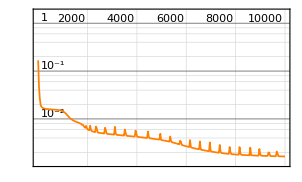
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:10000  rounds:10000  time:19s  examples/s:16893
data | ,,  training examples:31  processed examples:310000  skipped examples:0
method | ,,  ADAMoptimizer  batch size31CPU
round | ,,  loss:1.64×10^-3
 | rounds
loss | -Graphics- | 
 | ]

| rounds
loss | -Graphics-

544.922

{ADAM,Beta1→0.9,Beta2→0.999,Epsilon→1/100000,GradientClipping→None,L2Regularization→None,LearningRate→Automatic,LearningRateSchedule→None,WeightClipping→None}

NetChain[…]

NetGraph[…]

```mathematica
noisyData=Table[x->Exp[-x^2]+RandomVariate[NormalDistribution[0,.15]],{x,-3,3,.2}];

mlp=NetChain[{150,Tanh,150,Tanh,1}]

mlpTrainingResults=NetTrain[mlp,noisyData,All]

mlpTrainingResults["LossPlot"]
mlpTrainingResults["MeanBatchesPerSecond"]
mlpTrainingResults["OptimizationMethod"]
mlpTrainingResults["TrainedNet"]
mlpTrainingResults["TrainingNet"]
```

code 5.9

(* The code generates a synthetic dataset with added noise based on a Gaussian distribution. A neural network architecture with two hidden layers, each comprising 150 units with Tanh activation functions, is then defined. The code demonstrates three different methods for reporting training progress of the neural network using the noisy dataset: panel training progress reporting, progress indicator training progress reporting, and print training progress reporting. These methods offer various ways to monitor the training progress interactively, visually, or through printed updates: *)

```mathematica
noisyData=Table[x->Exp[-x^2]+RandomVariate[NormalDistribution[0,.15]],{x,-3,3,.2}];

mlp=NetChain[{150,Tanh,150,Tanh,1}]

PanelTrainingProgressReporting=NetTrain[mlp,noisyData,TrainingProgressReporting->"Panel"];
ProgressIndicatorTrainingProgressReporting=NetTrain[mlp,noisyData,TrainingProgressReporting->"ProgressIndicator"];
PrintTrainingProgressReporting=NetTrain[mlp,noisyData,TrainingProgressReporting->"Print"];
```

NetChain[…]

Starting training.

Optimization Method: ADAM
Beta1: 9.00*^-1
Beta2: 9.99*^-1
Epsilon: 1.00*^-5
Gradient Clipping:  —
L2 Regularization:  —
Learning Rate: Automatic
Learning Rate Schedule:  —
Weight Clipping:  —

Device: CPU

Batch Size: 31

Batches Per Round: 1

Training Examples: 31

%   round  batch   examples     inputs   learning       time       time    current      round

/10000     /1  processed    /second       rate    elapsed       left       loss       loss

8     843      1      26133      14604   7.55*^-4         2s        22s   2.81*^-2   1.05*^-2

18    1792      1      55552      15934   9.13*^-4         4s        18s   8.94*^-3   7.60*^-3

27    2748      1      85188       6810   9.67*^-4         6s        16s   7.25*^-3   6.43*^-3

37    3703      1     114793      16993   9.88*^-4         8s        14s   6.19*^-3   5.60*^-3

46    4647      1     144057      12684   9.95*^-4        10s        12s   5.41*^-3   4.95*^-3

55    5505      1     170655      16448   9.98*^-4        12s        10s   4.53*^-3   3.77*^-3

65    6505      1     201655      13407   9.99*^-4        14s         8s   3.56*^-3   3.29*^-3

74    7447      1     230857       7241   10.0*^-4        16s         5s   3.16*^-3   2.84*^-3

84    8369      1     259439      16115   10.0*^-4        18s         4s   2.58*^-3   2.16*^-3

92    9191      1     284921      11696   10.0*^-4        20s         2s   1.85*^-3   1.48*^-3

99    9908      1     307148      14850   10.0*^-4        22s         0s   1.42*^-3   1.30*^-3

code 5.10

(* The code demonstrates the process of training a neural network to solve a least- squares problem and monitoring its progress visually. Initially, synthetic data is generated based on a predefined function, and a neural network architecture is defined with specific layers and activation functions. Rather than using the default progress panel, the code dynamically updates and displays a plot illustrating the behavior of the network during training, overlaying the original data with the network’s output in red. Training progress is monitored using this custom plot, providing real-time feedback on the network’s performance. After a specified duration of training, the trained network is plotted to visualize its performance on the data: *)

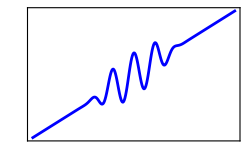

NetChain[…]

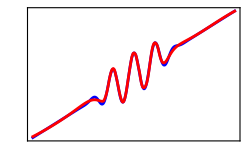

```mathematica
trainingData=Table[
x->Cos[10x]*Exp[-x^4]+x,
{x,-3,3,.02}
];

visualizeData[points_,color_]:=ListLinePlot[
points,
PlotStyle->color,
FrameTicks->False,
PlotRangePadding->0.1,
Frame->True,
PlotRange->All,
ImageSize->250
]

originalPlot=visualizeData[trainingData[[All,2]],Blue]

net=NetChain[
{20,Ramp,30,Tanh,30,Tanh,1},
"Input"->"Scalar",
"Output"->"Scalar"
];

plotTrainingProgress[net_,t_]:=Show[
originalPlot,
visualizeData[net@Range[-3,3,.02],Red],
Epilog->Text[t,{10,0.9},{-1,0}],
ImageSize->250
]

trainedNet=NetTrain[
net,
trainingData,
MaxTrainingRounds->Quantity[10,"Seconds"],
TrainingProgressReporting->{
plotTrainingProgress[#Net,#AbsoluteBatch]&, 
"Interval"->0.1
}
]

plotTrainingProgress[trainedNet,""]
```

### Monitor Saturation and Vanishing Gradients During Training

code 5.11

(* The code generates a neural network configuration with randomized weights and biases within specified boundaries using Mathematica’s NetChain. It then generates random input data within user-defined boundaries and applies the neural network to produce corresponding outputs, utilizing either a logistic sigmoid or hyperbolic tangent activation function chosen by the user. The results are visualized through a plot depicting the input data and neural network outputs, aiding in understanding the impact of activation function saturation on the data. Through interactive controls, users can adjust parameters such as random seed, weight and bias boundaries, input data boundaries, and activation function, facilitating exploration of different scenarios and their effects on the neural network’s behavior: *)

```mathematica
Manipulate[
SeedRandom[randomSeed];
weight=RandomReal[{minWeight,maxWeight}];
bias=RandomReal[{minBias,maxBias}];
neuralNet=NetChain[
{
LinearLayer[1,"Weights"->weight,"Biases"->bias],
ElementwiseLayer[activationFunction]
},
"Input"->1
];
inputData=RandomReal[{minInput,maxInput},{100,1}];
outputData=neuralNet[inputData];

ListPlot[
Transpose[
{Flatten[inputData],Flatten[outputData]}],
PlotStyle->{PointSize[0.02],Purple},
PlotRange->All,
Frame->True,
FrameLabel->{"Input","Output"},
PlotLegends->Placed[{"Output"},{0.8,0.2}],
PlotLabel->"Activation Function Saturation with\n One-Dimensional Input",
ImageSize->250
],
{{randomSeed,1,"Random Seed"},1,1000,1,Appearance->"Labeled"},
{{minWeight,-5,"Min Weight"},-10,0,0.1,Appearance->"Labeled"},
{{maxWeight,5,"Max Weight"},0,10,0.1,Appearance->"Labeled"},
{{minBias,-2,"Min Bias"},-5,0,0.1,Appearance->"Labeled"},
{{maxBias,2,"Max Weight"},0,5,0.1,Appearance->"Labeled"},
{{minInput,-10,"Min Input"},-20,0,1,Appearance->"Labeled"},
{{maxInput,10,"Max Input"},0,20,1,Appearance->"Labeled"},
{{activationFunction,LogisticSigmoid,"Activation Function"},
{LogisticSigmoid,Tanh},ControlType->PopupMenu}
]
```

code 5.12

(* The code generates synthetic input-output data and constructs a neural network with multiple layers, each employing logistic sigmoid activation functions. It then trains the network using the generated data, tracking activation output statistics during training. The code visualizes the mean activation values with error bars for each hidden layer over training epochs, providing insights into activation behavior and potential saturation. Additionally, histograms are created to visualize the distribution of activation values for each layer, aiding in understanding activation characteristics: *)

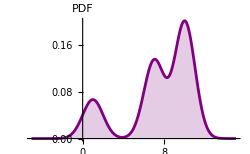

NetGraph[…]

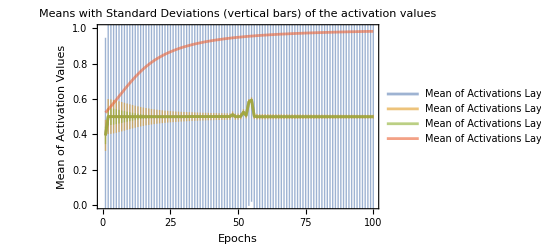

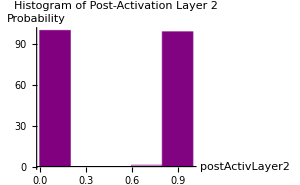
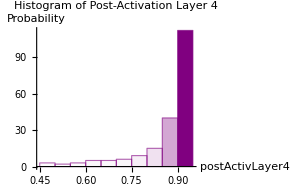
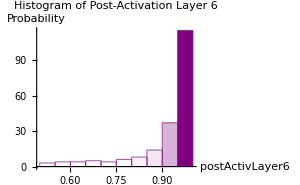
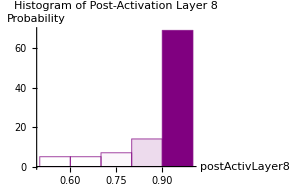

```mathematica
distribution=MixtureDistribution[{1,2,3},{NormalDistribution[1,1],
NormalDistribution[7,1],NormalDistribution[10,1]}];

inputData=RandomVariate[distribution,{2000,200}];
outputData=RandomReal[2,{2000,1}];

Plot[
Evaluate[PDF[distribution,x]],
{x,-5,15},
PlotRange->All,
Filling->Axis,
PlotStyle->Purple,
ImageSize->250,
AxesLabel->{None,"PDF"}
]

neuralNet=NetGraph[
{
2,LogisticSigmoid,
2,LogisticSigmoid,
2,LogisticSigmoid,
1,LogisticSigmoid
},
{1->2->3->4->5->6->7->8},
"Input"->200
];

initializedNet=NetInitialize[
neuralNet,
Method->{"Random","Weights"->0.1,"Biases"->0.1},
RandomSeeding->Automatic
]

trainingResults=NetTrain[
initializedNet,
<|"Input"->inputData,"Output"->outputData|>,
All,
MaxTrainingRounds->100,
TrainingProgressMeasurements->{
<|"Measurement"->NetPort[{2,"Output"}],"Interval"->"Round"|>,
<|"Measurement"->NetPort[{4,"Output"}],"Interval"->"Round"|>,
<|"Measurement"->NetPort[{6,"Output"}],"Interval"->"Round"|>,
<|"Measurement"->NetPort[{8,"Output"}],"Interval"->"Round"|>
}
];

trainingData=trainingResults["RoundMeasurementsLists"];

activationOutputLayer2=Values[trainingData][[2]];
activationOutputLayer4=Values[trainingData][[3]];
activationOutputLayer6=Values[trainingData][[4]];
activationOutputLayer8=Values[trainingData][[5]];

meanLayer2=Mean/@activationOutputLayer2;
stdDevLayer2=StandardDeviation/@activationOutputLayer2;
meanWithStdDevLayer2=Around@@@Transpose[{meanLayer2,stdDevLayer2}];

meanLayer4=Mean/@activationOutputLayer4;
stdDevLayer4=StandardDeviation/@activationOutputLayer4;
meanWithStdDevLayer4=Around@@@Transpose[{meanLayer2,stdDevLayer4}];

meanLayer6=Mean/@activationOutputLayer6;
stdDevLayer6=StandardDeviation/@activationOutputLayer6;
meanWithStdDevLayer6=Around@@@Transpose[{meanLayer2,stdDevLayer6}];

meanLayer8=Mean/@activationOutputLayer8;

ListLinePlot[
{meanWithStdDevLayer2,meanWithStdDevLayer4,meanWithStdDevLayer6,meanLayer8},
PlotStyle->{Opacity[0.6],Opacity[0.6],Opacity[0.6],Opacity[0.6]},
PlotRange->{0,1},
PlotLegends->{
"Mean of Activations Layer 2",
"Mean of Activations Layer 4",
"Mean of Activations Layer 6",
"Mean of Activations Layer 8"
},
IntervalMarkers->"Bars",
Frame->True,
FrameLabel->{"Epochs","Mean of Activation Values"},
PlotLabel->"Means with Standard Deviations (vertical bars)\n of the activation values"
]

Table[
Histogram[
Flatten[layer[[3]]],
Automatic,
"Count",
PlotLabel->Style[Row[{"Histogram of ",layer[[2]]}]],
AxesLabel->{layer[[1]],"Probability"},
ColorFunction->Function[{height},Opacity[height]],
ChartStyle->Purple,
ImageSize->300
],
{layer,{
{"postActivLayer2","Post-Activation Layer 2",activationOutputLayer2},
{"postActivLayer4","Post-Activation Layer 4",activationOutputLayer4},
{"postActivLayer6","Post-Activation Layer 6",activationOutputLayer6},
{"postActivLayer8","Post-Activation Layer 8",activationOutputLayer8}
}
}
]
```

code 5.13

(* The code aims to train a neural network to learn a mapping from two-dimensional input points to their respective exponential distances from the origin. It first generates a dataset comprising pairs of input points and their corresponding exponential distances. Then, it defines a neural network architecture with multiple layers, consisting of logistic sigmoid activation functions. The network is initialized with random weights and biases for reproducibility. Subsequently, the NetTrain function is utilized to train the network on the dataset. Training progress is monitored using the “GradientsRMS” property, and an evolution plot is generated to visualize the progress of gradients over training batchs. The training process is limited to 10 rounds with a batch size of 1024. The “GradientsRMS” property in NetTrain helps track the magnitudes of gradients for each layer during training, providing insights into the occurrence of vanishing gradients and their impact on training performance. Significantly smaller RMS values of gradients in earlier layers compared to deeper layers indicate the presence of the vanishing gradient problem. This information can guide adjustments to the network architecture or training parameters to mitigate the issue: *)

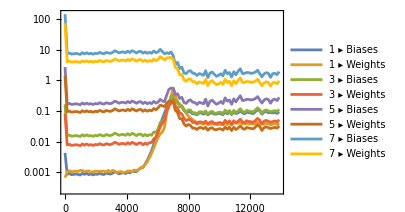

```mathematica
trainingData=Flatten@Table[{x,y}->{Exp[-Norm[{x,y}]]},{x,-3,3,.005},{y,-3,3,.005}];

neuralNet=NetChain[
{
10,LogisticSigmoid,
5,LogisticSigmoid,
5,LogisticSigmoid,
1
},
"Input"->2
];

initializedNet=NetInitialize[
neuralNet,
Method->{"Random","Weights"->0.05,"Biases"->0.05},
RandomSeeding->Automatic
];

NetTrain[
initializedNet,
trainingData,
<|
"Property"->"GradientsRMS",
"Form"->"EvolutionPlot",
"PlotOptions"->{ScalingFunctions->"Log",ImageSize->300},
"Interval"->"Batch"
|>,
MaxTrainingRounds->10,
BatchSize->1024
]
```

code 5.14

(* We can update the previous version of the code by changing the parameter ‘Interval’ to ‘Rounds’ and removing the ‘ScalingFunctions->”Log”’ option from the ‘PlotOptions’: *)

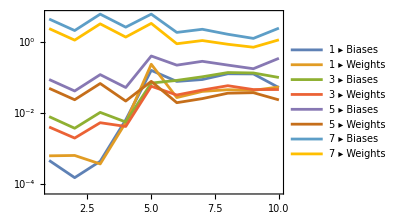

```mathematica
trainingData=Flatten@Table[{x,y}->{Exp[-Norm[{x,y}]]},{x,-3,3,.005},{y,-3,3,.005}];

neuralNet=NetChain[
{
10,LogisticSigmoid,
5,LogisticSigmoid,
5,LogisticSigmoid,
1
},
"Input"->2
];

initializedNet=NetInitialize[
neuralNet,
Method->{"Random","Weights"->0.05,"Biases"->0.05},
RandomSeeding->Automatic
];

NetTrain[
initializedNet,
trainingData,
<|
"Property"->"GradientsRMS",
"Form"->"EvolutionPlot",
"PlotOptions"->{ImageSize->300},
"Interval"->"Rounds"
|>,
MaxTrainingRounds->10,
BatchSize->1024
]
```

code 5.15

(* The code aims to train a neural network to learn the relationship between two- dimensional input points and their corresponding exponential distances from the origin. It achieves this by generating a dataset containing these pairs and defining a neural network architecture with multiple layers and logistic sigmoid activation functions. The network is then initialized with random weights and biases before being trained on the dataset. During training, the evolution of the root mean square (RMS) values of the weights for each layer is monitored to visualize the training progress and diagnose potential issues such as vanishing gradients. The training process is limited to 10 rounds with a batch size of 1024. Monitoring the RMS values of the weights for each layer of the neural network provides insights into how the weights are being adjusted during training. If the RMS values of the weights do not change significantly over time (i.e., they remain relatively constant or change only minimally), it suggests that the gradients in those layers are small. This indicates that the network is experiencing difficulty in learning meaningful representations or updating the parameters effectively in those layers. Small changes in the RMS values of the weights imply that the gradients are not providing sufficiently strong signals to guide meaningful updates to the weights. This situation often indicates the presence of vanishing gradients: *)

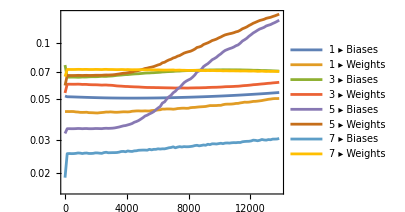

```mathematica
trainingData=Flatten@Table[{x,y}->{Exp[-Norm[{x,y}]]},{x,-3,3,.005},{y,-3,3,.005}];

neuralNet=NetChain[
{
10,LogisticSigmoid,
5,LogisticSigmoid,
5,LogisticSigmoid,
1
},
"Input"->2
];

initializedNet=NetInitialize[
neuralNet,
Method->{"Random","Weights"->0.05,"Biases"->0.05},
RandomSeeding->Automatic
];

NetTrain[
initializedNet,
trainingData,
<|
"Property"->"WeightsRMS",
"Form"->"EvolutionPlot",
"PlotOptions"->{ScalingFunctions->"Log",ImageSize->300},
"Interval"->"Batch"
|>,
MaxTrainingRounds->10,
BatchSize->1024
]
```

code 5.16

(* The code aims to analyze the behavior of gradients during the training of a neural network designed to learn the mapping from two-dimensional input points to their corresponding exponential distances from the origin. It first generates a dataset comprising pairs of input points and their exponential distances, then defines a neural network architecture with multiple layers, including logistic sigmoid activation functions. The code trains the network on the dataset while monitoring the gradients of network parameters, particularly focusing on the first and last layers, to assess their distributions and changes over training epochs. Visualization and statistical analysis of gradient distributions provide insights into the training dynamics, including potential issues such as vanishing or exploding gradients: *)

-Graphics3D-

-Graphics3D-

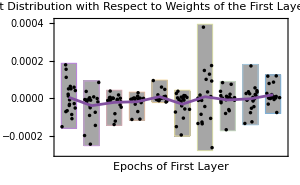

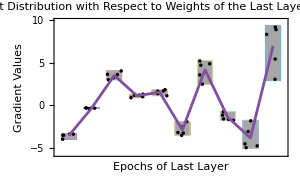

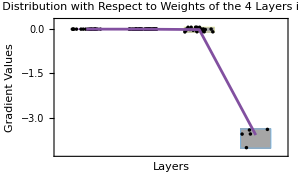

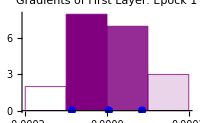
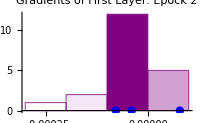
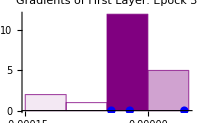
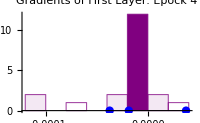
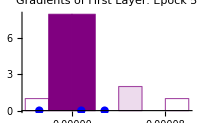

```mathematica
trainingData=Flatten@Table[
{x,y}->{Exp[-Norm[{x,y}]]},
{x,-3,3,.005},
{y,-3,3,.005}
];

neuralNet=NetChain[
{
10,LogisticSigmoid,
5,LogisticSigmoid,
5,LogisticSigmoid,
1
},
"Input"->2
];

initializedNet=NetInitialize[
neuralNet,
Method->{"Random","Weights"->0.05,"Biases"->0.05},
RandomSeeding->Automatic
];

gradients=NetTrain[
initializedNet,
trainingData,
<|
"Property"->"Gradients",
"Interval"->"Rounds"
|>,
MaxTrainingRounds->10,
BatchSize->1024
];

firstLayerGradientsData=Table[
Flatten[
Table[
Values[gradients][[i]][[2]],
{i,1,10}][[j]]
],
{j,1,10}]//Normal;

lastLayerGradientsData=Table[
Flatten[
Table[
Values[gradients][[i]][[8]],
{i,1,10}][[j]]
],
{j,1,10}]//Normal;

smoothKernelFirstLayer=SmoothKernelDistribution[#]&/@firstLayerGradientsData;

smoothKernelLastLayer=SmoothKernelDistribution[#]&/@lastLayerGradientsData;

ListLinePlot3D[
Table[
{(#-1),x,PDF[smoothKernelFirstLayer[[#]],x]},
{x,-0.001,0.001,0.0001}
]&/@{1,2,3,4,5,6,7,8,9,10},
Filling->Bottom,
FillingStyle->Opacity[0.75],
Joined->True,
BoxRatios->{1,1,1},
PlotRange->All,
ImageSize->250,
AxesLabel->{"Epoch","Gradient Value","Density"},
PlotLabel->"Densities of the First Layer Gradients"
]

ListLinePlot3D[
Table[
{(#-1),x,PDF[smoothKernelLastLayer[[#]],x]},
{x,-0.001,0.001,0.0001}
]&/@{1,2,3,4,5,6,7,8,9,10},
Filling->Bottom,
FillingStyle->Opacity[0.75],
Joined->True,
BoxRatios->{1,1,1},
PlotRange->All,
ImageSize->250,
AxesLabel->{"Epoch","Gradient Value","Density"},
PlotLabel->"Densities of the Last Layer Gradients"
]

firstLayerWeightsGradientData=Table[
Flatten[
Table[
Values[gradients][[i]][[2]],
{i,1,10}][[j]]
],
{j,1,10}]//Normal;

DistributionChart[
firstLayerWeightsGradientData,
Joined->"Mean",
ChartElementFunction->"PointDensity",
ChartStyle->"Pastel",
ImageSize->300,
FrameLabel->{"Epochs of First Layer","Gradient Values"},
PlotLabel->"Gradient Distribution with Respect \n to Weights of the First Layer for 10 Epochs"
]

firstLayerWeightsGradientData=Table[
Flatten[
Table[
Values[gradients][[i]][[8]],
{i,1,10}][[j]]
],
{j,1,10}]//Normal;

DistributionChart[
firstLayerWeightsGradientData,
Joined->"Mean",
ChartElementFunction->"PointDensity",
ChartStyle->"Pastel",
ImageSize->300,
FrameLabel->{"Epochs of Last Layer","Gradient Values"},
PlotLabel->"Gradient Distribution with Respect \n to Weights of the Last Layer for 10 Epochs"
]

firstEpochLayerWeightsGradientData=Table[
Flatten[
Table[
Values[gradients][[1]][[i]],
{i,2,8,2}
][[j]]
],
{j,1,4}]//Normal;

DistributionChart[
firstEpochLayerWeightsGradientData,
Joined->"Mean",
ChartElementFunction->"PointDensity",
ChartStyle->"Pastel",
ImageSize->300,
FrameLabel->{"Layers","Gradient Values"},
PlotLabel->"Gradient Distribution with Respect \n to Weights of the 4 Layers in the First Epoch"
]

Table[
Table[
Histogram[
data=Flatten[
Table[
Values[gradients][[i]][[k[[2]]]],
{i,1,10}
][[j]]
]//Normal,
Automatic,
Epilog->{
Blue,
PointSize[0.03],
Point[{
{StandardDeviation[data],0},
{Mean[data],0},
{-StandardDeviation[data],0}
}]
},
ColorFunction->Function[{height},Opacity[height]],
ChartStyle->Purple,
ImageSize->200,
PlotRange->Full,
PlotLabel->Style[Row[{"Gradients of ",k[[1]],": Epock ",j}]]
],
{j,1,10}
],
{k,{{"First Layer",2},{"Last Layer",8}}}
]
```

### NetInitialize (Xavier and Kaiming)

code 5.17

(* This code defines a function xavierInitialize which takes the number of input neurons (nIn) and the number of output neurons (nOut) as arguments. It then computes the scaling factor according to the Xavier initialization formula and generates random weights using that scale. Finally, it returns the initialized weights as a matrix with dimensions (nOut,nIn). The code will generate both a plot showing the distribution of weights and a histogram displaying the frequency of different weight values. The RandomVariate function is used to generate weights from a uniform distribution with min=-scale and max=scale: *)

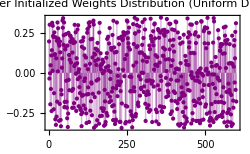

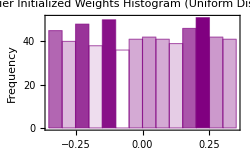

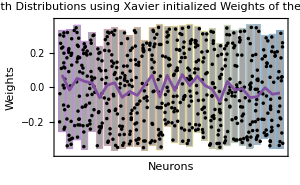

-Graphics3D-

```mathematica
xavierInitialize[nIn_,nOut_]:=Module[
{scale},
scale=Sqrt[6/(nIn+nOut)];
RandomVariate[UniformDistribution[{-scale,scale}],{nOut,nIn}]
]

nIn=20;
nOut=30;

weights=xavierInitialize[nIn,nOut];

ListPlot[
Flatten[weights],
PlotRange->All,
Filling->Axis,
PlotStyle->{PointSize[Tiny],Purple},
Frame->True,
ImageSize->250,
FrameLabel->{"Index","Weight"},
PlotLabel->"Xavier Initialized Weights Distribution \n(Uniform Distribution)"
]

Histogram[
Flatten[weights],
20,
PlotRange->All,
Frame->True,
ColorFunction->Function[{height},Opacity[height]],
ChartStyle->Purple,
ImageSize->250,
FrameLabel->{"Weigth","Frequency"},
PlotLabel->"Xavier Initialized Weights Histogram \n(Uniform Distribution)"
]

DistributionChart[
weights,
Joined->"Mean",
ChartElementFunction->"PointDensity",
ChartStyle->"Pastel",
ImageSize->300,
FrameLabel->{"Neurons","Weights"},
PlotLabel->"Weigth Distributions using Xavier initialized Weights \n of the 30 Neurons"
]

smoothKernelLastLayer=SmoothKernelDistribution[#]&/@weights;

ListLinePlot3D[
Table[
{(#-1),x,PDF[smoothKernelLastLayer[[#]],x]},
{x,-0.5,0.5,.01}
]&/@Range[1,30],
Filling->Bottom,
Joined->True,
BoxRatios->{1, 1, 1},
PlotRange->All,
ImageSize->300,
AxesLabel->{"Neurons","Weights","Density"},
PlotLabel->"Weight Distributions using Xavier initialized \n Weights of the 30 Neurons"
]
```

code 5.18

(* In this version, the RandomVariate function is used to generate weights from a normal distribution with mean 0 and standard deviation calculated according to the Xavier initialization formula. The rest of the code remains the same as before, generating both a plot and a histogram of the weight distribution: *)

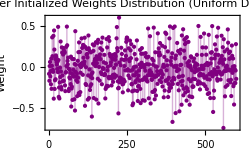

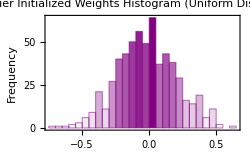

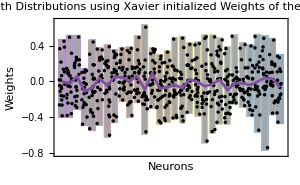

-Graphics3D-

```mathematica
xavierInitialize[nIn_,nOut_]:=Module[
{scale},
scale=Sqrt[1/nIn];
RandomVariate[NormalDistribution[0,scale],{nOut,nIn}]
]

nIn=20;
nOut=30;

weights=xavierInitialize[nIn,nOut];

ListPlot[
Flatten[weights],
PlotRange->All,
Filling->Axis,
PlotStyle->{PointSize[Tiny],Purple},
Frame->True,
ImageSize->250,
FrameLabel->{"Index","Weight"},
PlotLabel->"Xavier Initialized Weights Distribution \n(Uniform Distribution)"
]

Histogram[
Flatten[weights],
20,
PlotRange->All,
Frame->True,
ColorFunction->Function[{height},Opacity[height]],
ChartStyle->Purple,
ImageSize->250,
FrameLabel->{"Weigth","Frequency"},
PlotLabel->"Xavier Initialized Weights Histogram \n(Uniform Distribution)"
]

DistributionChart[
weights,
Joined->"Mean",
ChartElementFunction->"PointDensity",
ChartStyle->"Pastel",
ImageSize->300,
FrameLabel->{"Neurons","Weights"},
PlotLabel->"Weigth Distributions using Xavier initialized Weights \n of the 30 Neurons"
]

smoothKernelLastLayer=SmoothKernelDistribution[#]&/@weights;

ListLinePlot3D[
Table[
{(#-1),x,PDF[smoothKernelLastLayer[[#]],x]},
{x,-0.5,0.5,.01}
]&/@Range[1,30],
Filling->Bottom,
Joined->True,
BoxRatios->{1, 1, 1},
PlotRange->All,
ImageSize->300,
AxesLabel->{"Neurons","Weights","Density"},
PlotLabel->"Weight Distributions using Xavier initialized \n Weights of the 30 Neurons"
]
```

code 5.19

(* This code defines a function kaimingInitialize which takes the number of input neurons (nIn), the number of output neurons (nOut), and optionally a distribution (defaulting to a normal distribution with mean 0 and standard deviation 1) as arguments. It then computes the scaling factor according to the Kaiming initialization formula and generates random weights from the specified distribution, scaled by this factor. Finally, it returns the initialized weights as a matrix with dimensions (nOut,nIn): *)

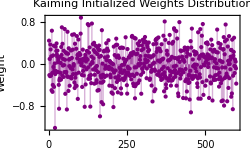

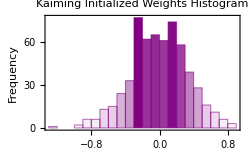

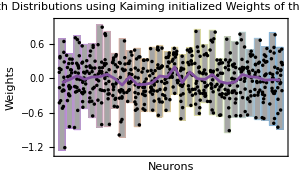

-Graphics3D-

```mathematica
kaimingInitialize[nIn_,nOut_,distribution_:NormalDistribution[0,1]]:=Module[
{scale},
scale=Sqrt[2/nIn];
RandomVariate[distribution,{nOut,nIn}]*scale
];

nIn=20;
nOut=30;

weights=kaimingInitialize[nIn,nOut];

ListPlot[
Flatten[weights],
PlotRange->All,
Filling->Axis,
PlotStyle->{PointSize[Tiny],Purple},
Frame->True,
ImageSize->250,
FrameLabel->{"Index","Weight"},
PlotLabel->"Kaiming Initialized Weights Distribution"
]

Histogram[
Flatten[weights],
20,
PlotRange->All,
Frame->True,
ColorFunction->Function[{height},Opacity[height]],
ChartStyle->Purple,
ImageSize->250,
FrameLabel->{"Weigth","Frequency"},
PlotLabel->"Kaiming Initialized Weights Histogram"
]

DistributionChart[
weights,
Joined->"Mean",
ChartElementFunction->"PointDensity",
ChartStyle->"Pastel",
ImageSize->300,
FrameLabel->{"Neurons","Weights"},
PlotLabel->"Weigth Distributions using Kaiming initialized Weights \n of the 30 Neurons"
]

smoothKernelLastLayer=SmoothKernelDistribution[#]&/@weights;

ListLinePlot3D[
Table[
{(#-1),x,PDF[smoothKernelLastLayer[[#]],x]},
{x,-0.5,0.5,.01}
]&/@Range[1,30],
Filling->Bottom,
Joined->True,
BoxRatios->{1, 1, 1},
PlotRange->All,
ImageSize->300,
AxesLabel->{"Neurons","Weights","Density"},
PlotLabel->"Weight Distributions using Kaiming initialized \n Weights of the 30 Neurons"
]
```

code 5.20

(* The code aims to explore the effects of different weight initialization methods, specifically Xavier initialization with uniform and normal distributions, on the weights of a simple neural network. Firstly, a network structure comprising an input layer of 30 units followed by two fully connected layers with 100 units each and a ReLU activation function is defined. Then, the network weights are initialized using Xavier initialization with uniform and normal distributions, yielding two separate sets of weights. Histograms of the weights in the first layer are plotted for both cases, providing visual insights into their distribution characteristics: *)

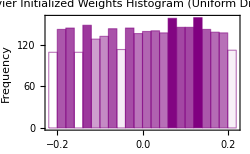

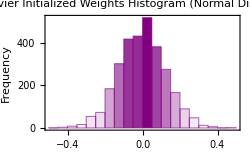

```mathematica
simpleNetwork=NetChain[
{
LinearLayer[100,"Input"->30],
Ramp,
LinearLayer[100]
}
];

initializedNetworkUniform=NetInitialize[
simpleNetwork,
Method->{"Xavier","Distribution"->"Uniform"}
];

weightsFirstLayerUniform=NetExtract[initializedNetworkUniform,{1,"Weights"}];

Histogram[
Flatten[weightsFirstLayerUniform],
20,
PlotRange->All,
ColorFunction->Function[{height},Opacity[height]],
ChartStyle->Purple,
ImageSize->250,
Frame->True,
FrameLabel->{"Weight","Frequency"},
PlotLabel->"Xavier Initialized Weights Histogram \n (Uniform Distribution"
]

initializedNetworkNormal=NetInitialize[
simpleNetwork,
Method->{"Xavier","Distribution"->"Normal"}
];

weightsFirstLayerNormal=NetExtract[initializedNetworkNormal,{1,"Weights"}];

Histogram[
Flatten[weightsFirstLayerNormal],
20,
PlotRange->All,
ColorFunction->Function[{height},Opacity[height]],
ChartStyle->Purple,
ImageSize->250,
Frame->True,
FrameLabel->{"Weight","Frequency"},
PlotLabel->"Xavier Initialized Weights Histogram \n (Normal Distribution"
]
```

code 5.21

(* The code generates synthetic data and defines a neural network architecture with two linear layers and a Tanh activation function, initializing the weights using Xavier initialization with a uniform distribution. It then trains the network using the generated data and visualizes the distribution of weights in the first layer before and after training via histograms. Additionally, it utilizes kernel density estimation to analyze the first layer weights over 10 epochs, providing insights into the training process’s stability and convergence: *)

NetChain[…]

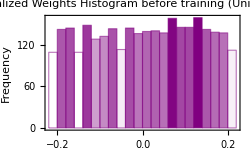

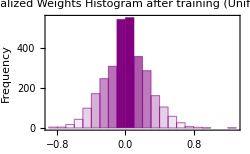

-Graphics3D-

```mathematica
data=Table[RandomReal[{-1,1},30]->UnitVector[2,RandomInteger[{1,2}]],{1000}];

net=NetChain[{LinearLayer[100,"Input"->30],Tanh,LinearLayer[2]}];

netInitialize=NetInitialize[net,Method->{"Xavier","Distribution"->"Uniform"}];
weightsFirstLayerbefore=NetExtract[netInitialize,{1,"Weights"}];

trainedNet=NetTrain[netInitialize,data]

weightsFirstLayerafter=NetExtract[trainedNet,{1,"Weights"}];

Histogram[
Flatten[weightsFirstLayerbefore],
20,
PlotRange->All,
ColorFunction->Function[{height},Opacity[height]],
ChartStyle->Purple,
ImageSize->250,
Frame->True,
FrameLabel->{"Weigtht","Frequency"},
PlotLabel->"Xavier Initialized Weights Histogram \n before training (Uniform Distribution)"
]

Histogram[
Flatten[weightsFirstLayerafter],
20,
PlotRange->All,
ColorFunction->Function[{height},Opacity[height]],
ChartStyle->Purple,
ImageSize->250,
Frame->True,
FrameLabel->{"Weigtht","Frequency"},
PlotLabel->"Xavier Initialized Weights Histogram \n after training (Uniform Distribution)"
]

weights=NetTrain[
netInitialize,
data,
<|
"Property"->"Weights",
"Interval"->"Rounds"
|>,
MaxTrainingRounds->10
];

firstLayerWeightsData=Table[
Flatten[
Table[
Values[weights][[i]][[2]],
{i,1,10}][[j]]
],
{j,1,10}]//Normal;

smoothKernelFirstLayer=SmoothKernelDistribution[#]&/@firstLayerWeightsData;

ListLinePlot3D[
Table[
{(#-1),x,PDF[smoothKernelFirstLayer[[#]],x]},
{x,-1,1,0.1}
]&/@Range[1,10],
Filling->Bottom,
FillingStyle->Opacity[0.75],
Joined->True,
BoxRatios->{1,1,1},
PlotRange->All,
ImageSize->250,
AxesLabel->{"Epoch","Weights","Density"},
PlotLabel->"Densities of the First Layer Weights \n for 10 Epochs"
]
```

### Feature Scaling: Standardize, Whitenend and Mahalanobis Distances

Standardize[list]	shifts and rescales the elements of list to have zero mean and unit sample variance.

Standardize[list,f1]	shifts the elements in list by f1[list] and rescales them to have unit sample variance.

Standardize[list,f1,f2] 	shifts by f1[list] and scales by f2[list].

Remarks:

• Standardize shifts by a location and rescales by a scale estimated from the elements of list.

• Standardize[list] is effectively (list-Mean[list])/StandardDeviation[list] for nonzero StandardDeviation[list].

• Standardize[list,f1] is effectively (list-f1[list])/StandardDeviation[list].

• Standardize[list,f1,f2] is effectively (list-f1[list])/f2[list].

code 5.22

```mathematica
sdata=Standardize[{6.5,3.8,6.6,5.7,6.0,6.4,5.3}]
{Mean[sdata],Variance[sdata]}
```

{0.75705,-1.99453,0.85896,-0.0582346,0.247497,0.655139,-0.465877}

{0.,1.}

code 5.23

(* The code defines a custom standardize function that standardizes numerical data by subtracting the mean and dividing by the standard deviation. It then utilizes the Simplify function to simplify expressions obtained by applying both the custom standardize function and the built-in Standardize function to a list of real numbers, {a,b,c}, aiming to validate the custom implementation against the built- in functionality and potentially gain insights into the simplification process: *)

```mathematica
standardize[data_]:=Module[
{mean,stdDev},
mean=Mean[data];
stdDev=StandardDeviation[data];
(data-mean)/stdDev
]

Simplify[standardize[{a,b,c}],{a,b,c}∈Reals]
Simplify[Standardize[{a,b,c}],{a,b,c}∈Reals]
```

{(2 a-b-c)/(√3 √(a^2+b^2-b c+c^2-a (b+c))),-(a-2 b+c)/(√3 √(a^2+b^2-b c+c^2-a (b+c))),-(a+b-2 c)/(√3 √(a^2+b^2-b c+c^2-a (b+c)))}

{(2 a-b-c)/(√3 √(a^2+b^2-b c+c^2-a (b+c))),-(a-2 b+c)/(√3 √(a^2+b^2-b c+c^2-a (b+c))),-(a+b-2 c)/(√3 √(a^2+b^2-b c+c^2-a (b+c)))}

code 5.24

(* The code generates 200 random values from a normal distribution with a mean of 4 and a standard deviation of 1, computes descriptive statistics such as mean and standard deviation for both the original and standardized data, and plots the original data with its mean and ±standard deviation bands as well as the standardized data with similar visualizations. By standardizing the data, the code allows for comparison between the original distribution and a standard normal distribution, providing insights into the normalization process and its effects on the data distribution: *)

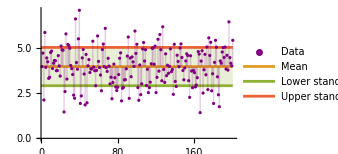

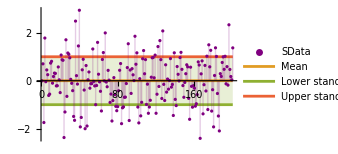

```mathematica
sampleData=RandomReal[NormalDistribution[4,1],200];

standardDeviation=StandardDeviation[sampleData];
meanValue=N[Mean[sampleData]];
dataLength=Length[sampleData];

standardizedData=Standardize[sampleData];
standardDeviationStandardized=StandardDeviation[standardizedData];
meanValueStandardized=N[Mean[standardizedData]];
dataLengthStandaridized=Length[standardizedData];

ListPlot[
{
sampleData,
{{0,meanValue},{dataLength,meanValue}},
{{0,meanValue-standardDeviation},{dataLength,meanValue-standardDeviation}},
{{0,meanValue+standardDeviation},{dataLength,meanValue+standardDeviation}}
},
Joined->{False,True,True,True},
Filling->{1->meanValue,3->{4}},
PlotStyle->{Purple,Automatic,Automatic,Automatic},
PlotLegends->{"Data","Mean","Lower standard deviation band","Upper standard deviation band"},
AxesLabel->Automatic,
ImageSize->250
]

ListPlot[
{
standardizedData,
{
{0,meanValueStandardized},
{dataLengthStandaridized,meanValueStandardized}
},
{
{0,meanValueStandardized-standardDeviationStandardized},
{dataLengthStandaridized,meanValueStandardized-standardDeviationStandardized}
},
{
{0,meanValueStandardized+standardDeviationStandardized},
{dataLengthStandaridized,meanValueStandardized+standardDeviationStandardized}
}
},
Joined->{False,True,True,True},
Filling->{1->meanValueStandardized,3->{4}},
PlotStyle->{Purple,Automatic,Automatic,Automatic},
PlotLegends->{"SData","Mean","Lower standard deviation band","Upper standard deviation band"},
AxesLabel->Automatic,
ImageSize->250
]
```

code 5.25

(* This code will generate three plots: one for the original data, one for the decorrelated data, and one for the whitened data. Additionally, it will print out the covariance matrix of original correlated data, eigenvalues, eigenvectors, covariance matrix of decorrelated data and covariance matrix of whitened data to help understand the transformation steps. Decorrelation is achieved by transforming the centered data with the eigenvectors. Whitening is done by scaling the decorrelated data by the inverse square root of eigenvalues: *)

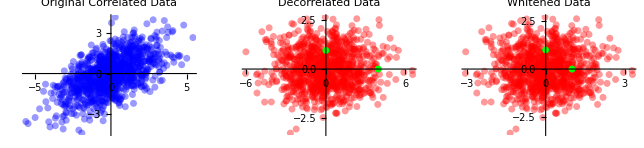

Eigenvalues: {3.94926,0.953016}

Eigenvectors: {{-0.822513,-0.568747},{0.568747,-0.822513}}

Covariance Matrix of Original Correlated Data: {{2.98006,1.40165},{1.40165,1.92222}}

Covariance Matrix of Decorrelated Data: {{3.94926,-6.76542×10^-17},{-6.76542×10^-17,0.953016}}

Covariance Matrix of Whitened Data: {{1.,-4.68375×10^-17},{-4.68375×10^-17,1.}}

```mathematica
SeedRandom[123];
originalData=RandomVariate[MultinormalDistribution[{0,0},{{3,1.5},{1.5,2}}],1000];

centeredData=(#-Mean[originalData])&/@originalData;
covarianceMatrix=Covariance[centeredData];
{eigenvalues,eigenvectors}=Eigensystem[covarianceMatrix];
decorrelatedData=centeredData.Transpose[eigenvectors];
whitenedData=decorrelatedData.DiagonalMatrix[1/Sqrt[eigenvalues]];

covDecorrelated=Covariance[decorrelatedData];
covWhitened=Covariance[whitenedData];

GraphicsRow[
{
ListPlot[
originalData,
PlotStyle->{PointSize[0.02],Opacity[0.4],Blue},
PlotLabel->"Original Correlated Data",
ImageSize->250
],
ListPlot[
decorrelatedData,
Epilog->{PointSize[0.02],Green,Point[covDecorrelated]},
PlotStyle->{PointSize[0.02],Opacity[0.4],Red},
PlotLabel->"Decorrelated Data",
ImageSize->250
],
ListPlot[
whitenedData,
Epilog->{PointSize[0.02],Green,Point[covWhitened]},
PlotStyle->{PointSize[0.02],Opacity[0.4],Red},
PlotLabel->"Whitened Data",
ImageSize->250
]
}
]

Print["Eigenvalues: ",eigenvalues];
Print["Eigenvectors: ",eigenvectors];
Print["Covariance Matrix of Original Correlated Data: ",covarianceMatrix];
Print["Covariance Matrix of Decorrelated Data: ",covDecorrelated];
Print["Covariance Matrix of Whitened Data: ",covWhitened];
```

code 5.26

(* The code generates a dataset from a bivariate normal distribution and conducts statistical analyses on it. Firstly, it whitens the data by removing the mean and scaling it using the inverse square root of the covariance matrix. Then, it calculates the Mahalanobis distances, which account for the covariance structure of the data, and Euclidean distances from each point to the mean. These distances are plotted for visualization alongside the original and whitened datasets, allowing for comparisons between Euclidean and Mahalanobis distances. The code provides insight into the effects of whitening on data distribution and the differences between Euclidean and Mahalanobis distance metrics in assessing data variability: *)

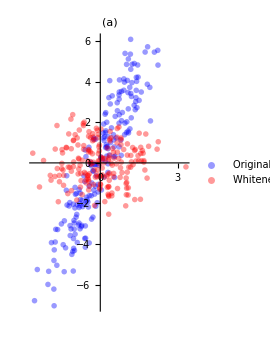

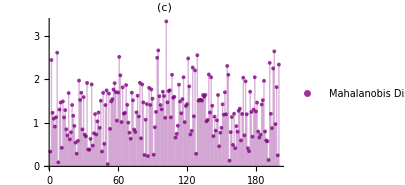

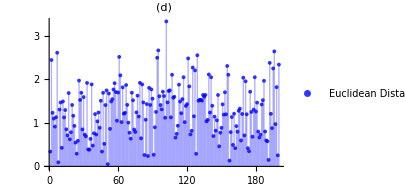

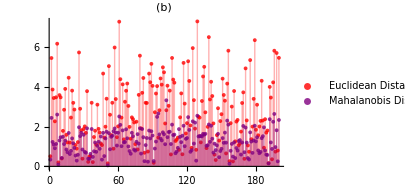

```mathematica
SeedRandom[23];
sampleData=RandomVariate[BinormalDistribution[{0,0},{1,3},0.9],200];

meanVector=Mean[sampleData];
covarianceMatrix=Covariance[sampleData];
inverseCovarianceMatrix=Inverse[covarianceMatrix];

matrixSquareRoot[X_]:=Module[
{eigenSystem},
eigenSystem=Eigensystem[X];
Transpose[eigenSystem[[2]]].DiagonalMatrix[Sqrt[eigenSystem[[1]]]].eigenSystem[[2]]
]

whitenedData=Transpose[matrixSquareRoot[inverseCovarianceMatrix].Transpose[(sampleData-ConstantArray[meanVector,Length[sampleData]])]];

mahalanobisDistance[x_,meanVec_,covMatrix_]:=Sqrt[(x-meanVec).Inverse[covMatrix].(x-meanVec)]

mahalanobisDistances=mahalanobisDistance[#,meanVector,covarianceMatrix]&/@sampleData;

euclideanDistances=EuclideanDistance[#,meanVector]&/@sampleData;
euclideanDistancesOfWhitened=EuclideanDistance[#,{0,0}]&/@whitenedData;

ListPlot[
{sampleData,whitenedData},
AspectRatio->1.7,
PlotRange->All,
PlotLegends->Placed[{"Original Data","Whitened Data"},{0.7,0.1}],
PlotStyle->{{PointSize[0.02],Opacity[0.4],Blue},{PointSize[0.02],Opacity[0.4],Red}},
PlotLabel->"(a)",
ImageSize->200
]

mahalanobisDistancesPlot=ListPlot[
mahalanobisDistances,
Filling->Axis,
PlotStyle->{Opacity[0.8],Purple},
PlotLabel->"(c)",
PlotRange->Full,
PlotLegends->Placed[{"Mahalanobis Distances of Original Data"},{0.5,0.9}],
ImageSize->300
]

euclideanDistancesPlot=ListPlot[
euclideanDistances,
Filling->Axis,
PlotStyle->{Opacity[0.8],Red},
PlotRange->All,
PlotLegends->Placed[{"Euclidean Distances of Original Data"},{0.5,0.8}],
ImageSize->300
];

euclideanDistancesOfWhitenedPlot=ListPlot[
euclideanDistancesOfWhitened,
Filling->Axis,
PlotStyle->{Opacity[0.8],Blue},
PlotLabel->"(d)",
PlotRange->Full,
PlotLegends->Placed[{"Euclidean Distances of Whitened Data"},{0.5,0.9}],
ImageSize->300
]

Show[{euclideanDistancesPlot,mahalanobisDistancesPlot},PlotLabel->"(b)"]
```

### BatchNormalizationLayer

MovingAverage[list,r]	gives the moving average of list, computed by averaging runs of r elements.

MovingAverage[list,{w1,w2,…,wr}] gives the moving average of list, computed with weights wi.

ExponentialMovingAverage[list,α]	gives the exponential moving average of list with smoothing constant α.

MovingMedian[list,r]	gives the moving median of list, computed using spans of r elements.

MovingMap[f,data,w]		applies f to size w windows in the specified data.

MovingMap[f,data,wspec]	uses windows specified by wspec.

Remarks:

• MovingAverage[list,r] gives a list of the means of elements in list taken in blocks of length r.

• MovingAverage gives a list of length Length[list]-r+1.

• The smoothing constant α is typically a number between 0 and 1, but can be any expression.

• ExponentialMovingAverage[x,α] generates a list of results in which .

• The output from ExponentialMovingAverage[list,α] has the same length as list.

• MovingMedian gives a list of the medians of elements in list taken in blocks of length r.

• MovingMedian gives a list of length Length[list]-r+1.

code 5.27

```mathematica
MovingAverage[{a,b,c,d,e},2]
MovingAverage[{a,b,c,d,e},{1,2}]
```

{(a+b)/2,(b+c)/2,(c+d)/2,(d+e)/2}

{1/3 (a+2 b),1/3 (b+2 c),1/3 (c+2 d),1/3 (d+2 e)}

code 5.28

```mathematica
MovingAverage[{1,5,7,3,6,2},3]
MovingAverage[{1.2,5.2,3.4,4.5,2.3,4.5},3]
```

{13/3,5,16/3,11/3}

{3.26667,4.36667,3.4,3.76667}

code 5.29

(* The goal of this code is to generate a dataset with noisy fluctuations, then smooth out these fluctuations using a moving average filter, and finally visualize both the original noisy data and the smoothed data: *)

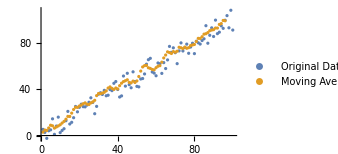

```mathematica
noisyData=Range[100]+RandomReal[{-10,10},100];
smoothedData=MovingAverage[noisyData,5];

ListPlot[
{noisyData,smoothedData},
ImageSize->250,
PlotLegends->Placed[{"Original Data","Moving Average Data"},{0.7,0.3}]
]
```

code 5.30

(* The code generates synthetic data with random noise added to a constant array, mimicking real-world data fluctuations. It then calculates moving averages for different window sizes (ranging from 10 to 40) to smooth out the data and highlight underlying trends. Finally, it plots the original data alongside the moving averages, offering a visual representation of the trend and the effectiveness of different window sizes in capturing the underlying patterns: *)

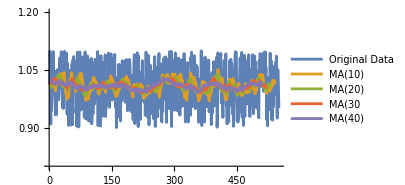

```mathematica
initialData=ConstantArray[1.,550]+RandomReal[{-0.1,0.1},550];
movingAverages=Table[
MovingAverage[initialData,WindowSizes],
{WindowSizes,10,40,10}
];

plotData=Prepend[movingAverages,initialData[[1;;550]]];

ListLinePlot[
plotData,
PlotRange->{0.8,1.2},
PlotLegends->{"Original Data","MA(10)","MA(20)","MA(30","MA(40)"},
ImageSize->300]
```

code 5.31

```mathematica
ExponentialMovingAverage[{a,b,c},α]
ExponentialMovingAverage[Range[10],1/3]
```

{a,-a (-1+α)+b α,c α-(-1+α) (-a (-1+α)+b α)}

{1,4/3,17/9,70/27,275/81,1036/243,3773/729,13378/2187,46439/6561,158488/19683}

code 5.32

(* The goal of this code is to generate a dataset with noisy fluctuations, then smooth out these fluctuations using an Exponential Moving Average filter, and finally visualize both the original noisy data and the smoothed data: *)

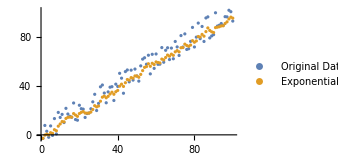

```mathematica
noisyData=Range[100]+RandomReal[{-10,10},100];
smoothedData=ExponentialMovingAverage[noisyData,0.25];

ListPlot[
{noisyData,smoothedData},
ImageSize->250,
PlotLegends->Placed[{"Original Data","Exponential Moving"},{0.7,0.25}]]
```

code 5.33

(* The code generates synthetic data with random noise added to a constant array, mimicking real-world data fluctuations. It then calculates Exponential Moving Average for different smoothing constants (0.1, 0.3 and 0.6) to smooth out the data and highlight underlying trends. Finally, it plots the original data alongside the Exponential Moving Average, offering a visual representation of the trend and the effectiveness of different smoothing constants in capturing the underlying patterns: *)

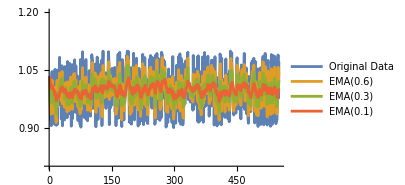

```mathematica
initialData=ConstantArray[1.,550]+RandomReal[{-0.1,0.1},550];
exponentialMovingAverage=Table[
ExponentialMovingAverage[initialData,smoothingconstant],
{smoothingconstant,{0.6,0.3,0.1}}
];

plotData=Prepend[exponentialMovingAverage,initialData[[1;;550]]];

ListLinePlot[
plotData,
PlotRange->{0.8,1.2},
PlotLegends->{"Original Data","EMA(0.6)","EMA(0.3)","EMA(0.1)"},
ImageSize->300
]
```

code 5.34

```mathematica
ExponentialMovingAverage[{a,b,c,d},0]
ExponentialMovingAverage[{a,b,c,d},1]
```

{a,a,a,a}

{a,b,c,d}

code 5.35

(* The code aims to offer an interactive platform for exploring moving averages and exponential moving averages applied to synthetic data. By setting a random seed for reproducibility, it generates a dataset with adjustable sample size and introduces sliders to dynamically modify the window size of the moving averages. Through ListLinePlot, the original data, moving average, and exponential moving average are visually represented with distinct colors, aiding in comprehension. The interactive interface allows users to observe how changes in the random seed, sample size, and window size influence the smoothing effect on the data, facilitating a deeper understanding of these statistical techniques within a visual context: *)

```mathematica
Manipulate[
SeedRandom[seed];
initialData=ConstantArray[1.,numSamples]+RandomReal[{-0.1,0.1},numSamples];
movingAverage=MovingAverage[initialData,WindowSize];
exponentialMovingAverage=ExponentialMovingAverage[initialData,WindowSize/100];
plotData={initialData,movingAverage,exponentialMovingAverage};

ListLinePlot[
plotData,
PlotRange->{0.8,1.2},
PlotLegends->{"Original Data","Moving Average","Exponential Moving Average"},
PlotStyle->{Purple,Blue,Red},
ImageSize->350,
PlotLabel->Row[{"Moving Averages (Window Size: ",WindowSize,")"}]
],
{{seed,1234,"Random Seed"},1,10000,1,Appearance->"Labeled"},
{{numSamples,300,"Number of Samples"},50,1000,50,Appearance->"Labeled"},
{{WindowSize,10,"Window Size"},5,50,1,Appearance->"Labeled"}]
```

code 5.36

```mathematica
MovingMedian[{1,2,5,6,1,4,3},3]
```

{2,5,5,4,3}

code 5.37

(* The goal of this code is to generate a dataset with noisy fluctuations, then smooth out these fluctuations using a Moving Median filter, and finally visualize both the original noisy data and the smoothed data: *)

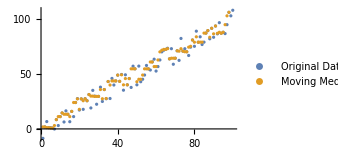

```mathematica
noisyData=Range[100]+RandomReal[{-10,10},100];
smoothedData=MovingMedian[noisyData,3];

ListPlot[
{noisyData,smoothedData},
ImageSize->250,
PlotLegends->Placed[{"Original Data","Moving Median"},{0.7,0.25}]]
```

code 5.38

```mathematica
data={Subscript[x,1],Subscript[x,2],Subscript[x,3],Subscript[x,4],Subscript[x,5],Subscript[x,6]};
MovingMap[Mean,data,Quantity[3,"Events"]]
MovingAverage[data,3]
```

{1/3 (x_1+x_2+x_3),1/3 (x_2+x_3+x_4),1/3 (x_3+x_4+x_5),1/3 (x_4+x_5+x_6)}

{1/3 (x_1+x_2+x_3),1/3 (x_2+x_3+x_4),1/3 (x_3+x_4+x_5),1/3 (x_4+x_5+x_6)}

code 5.39

```mathematica
data=RandomInteger[{-10,10},10]
MovingMap[Median,data,Quantity[3,"Events"]]
MovingMedian[data,3]
```

{-1,1,3,-5,5,-7,4,-2,-9,10}

{1,1,3,-5,4,-2,-2,-2}

{1,1,3,-5,4,-2,-2,-2}

code 5.40

```mathematica
data=RandomInteger[{-10,10},40]
MovingMap[Variance,data,Quantity[10,"Events"]]
```

{2,9,-5,10,-10,-2,7,2,5,-10,-1,-3,5,1,-10,0,8,4,-9,-6,-9,1,5,2,-3,-7,-5,-2,0,10,3,0,-3,1,-4,-4,-8,-10,-6,-1}

{2428/45,973/18,4121/90,1387/30,524/15,524/15,1562/45,3281/90,3409/90,749/18,3209/90,3769/90,85/2,85/2,1942/45,3121/90,1732/45,847/30,229/10,98/5,162/5,374/15,249/10,413/18,1012/45,2081/90,892/45,2141/90,65/2,341/10,748/45}

BatchNormalizationLayer[] 	represents a trainable net layer that normalizes its input data by learning the data mean and variance.

The following optional parameters can be included:

“Epsilon”	0.001` 	stability parameter

Interleaving	False 		the position of the channel dimension

“Momentum”	0.9 		momentum used during training

The following learnable arrays can be included:

“Biases”		Automatic	learnable bias array

“MovingMean”		Automatic	moving estimate of the mean

“MovingVariance”	Automatic	moving estimate of the variance

“Scaling”		Automatic	learnable scaling array

Remarks:

• With Automatic settings, the biases, scaling, moving mean and moving variance arrays are initialized automatically when NetInitialize or NetTrain is used.

• If biases, scaling, moving variance and moving mean have been set, BatchNormalizationLayer[…][input] explicitly computes the output from applying the layer.

• BatchNormalizationLayer[…][{input1,input2,…}] explicitly computes outputs for each of the inputi.

code 5.41

```mathematica
BatchNormalizationLayer[]
```

BatchNormalizationLayer[…]

code 5.42

```mathematica
batchnorm=NetInitialize@BatchNormalizationLayer["Input"->3]
NetExtract[batchnorm,"Biases"]//Normal
NetExtract[batchnorm,"Scaling"]//Normal
NetExtract[batchnorm,"MovingMean"]//Normal
NetExtract[batchnorm,"MovingVariance"]//Normal
NetExtract[batchnorm,"Epsilon"]
NetExtract[batchnorm,"Momentum"]

batchnorm[{2,3,4}]
```

BatchNormalizationLayer[…]

{0.,0.,0.}

{1.,1.,1.}

{0.,0.,0.}

{1.,1.,1.}

0.001

0.9

{1.999,2.9985,3.998}

code 5.43

(* The code initializes a custom BatchNormalizationLayer with explicitly specified parameters, including scaling factors, biases, epsilon value, momentum, and initial values for moving mean and variance. By setting these parameters, the code aims to customize the behavior of the BatchNormalizationLayer according to specific requirements or experimental setups. Subsequently, the layer is applied to an input vector to observe its normalization process and the resulting output, thereby demonstrating how the specified parameters influence the layer’s operation and its effect on input data normalization within neural network architectures: *)

```mathematica
batchnorm=NetInitialize@BatchNormalizationLayer[
"Scaling"->{1,1,1},
"Biases"->{1,-2,1},
"Epsilon"->0.1,
"Momentum"->0.1,
"MovingMean"->{2,2,2},
"MovingVariance"->{2,2,2}
]

batchnorm[{2,3,4}]
```

BatchNormalizationLayer[…]

{1.,-1.30993,2.38013}

code 5.44

(* The code initializes a BatchNormalizationLayer with specific parameters: “Scaling” is set to {0,0,0}, indicating no scaling, and “Biases” is set to {1,2,20}. The purpose is to demonstrate that when the layer is applied to any input data, it returns the values specified for the “Biases” parameter, disregarding the input entirely. This behavior showcases how the biases directly affect the output of the layer, irrespective of the input values: *)

```mathematica
batchnorm=NetInitialize@BatchNormalizationLayer[
"Scaling"->{0,0,0},
"Biases"->{1,2,20}
]

batchnorm[{1,2,3}]
batchnorm[{3,4,5}]
```

BatchNormalizationLayer[…]

{1.,2.,20.}

{1.,2.,20.}

code 5.45

(* The code presents two methods for conducting batch normalization: a custom function, batchNormalizationLayer, and Mathematica’s built-in BatchNormalizationLayer. The custom function is designed to manually compute batch normalization, allowing explicit control over parameters such as scaling, biases, moving means, and variances. Conversely, the built-in function streamlines the process by initializing a batch normalization layer with predefined parameters, offering a more concise and efficient solution. By manually computing batch normalization, we gain a deeper understanding of its inner workings. However, it’s important to note that in practice, deep learning frameworks like Mathematica provide efficient built-in implementations that handle the computation automatically, allowing for easier experimentation and faster training: *)

```mathematica
batchNormalizationLayer[input_,scalings_,biases_,movingMeans_,movingVariances_,epsilon_]:=Module[
{sd=Sqrt[movingVariances+epsilon]},
(scalings*(input-movingMeans)/sd+biases)
]

scalings=0.5;
biases=0.1;
movingMeans=0.2;
movingVariances=0.3;
epsilon=10^-5;
input=0.3;
normalizedOutput=batchNormalizationLayer[input,scalings,biases,movingMeans,movingVariances,epsilon]

batchnorm=NetInitialize@BatchNormalizationLayer[
"Scaling"->0.5,
"Biases"->0.1,
"Epsilon"->10^-5,
"MovingMean"->0.2,
"MovingVariance"->0.3,
"Input"->1
];

batchnorm[0.3]
```

0.191286

{0.191286}

code 5.46

(* The code aims to create an interactive environment for exploring the effects of batch normalization on a randomly generated dataset. It allows users to adjust parameters such as the number of samples, scaling, biases, epsilon, momentum, moving mean, moving variance, and random seed using sliders. The code generates a random dataset based on the specified parameters and applies a custom BatchNormalizationLayer to normalize the data. The original and normalized datasets are then plotted on a graph, with the original data represented in blue and the normalized data in red. This interactive visualization enables users to observe how changes in batch normalization parameters impact the distribution and normalization of the dataset, facilitating experimentation and understanding of batch normalization techniques: *)

```mathematica
Manipulate[
Module[
{data,normalizedData,batchnorm},
SeedRandom[seed];
data=RandomReal[{-10,10},{numberOfSamples,1}];
batchnorm=NetInitialize@BatchNormalizationLayer[
"Scaling"->scaling,
"Biases"->biases,
"Epsilon"->epsilon,
"Momentum"->momentum,
"MovingMean"->movingMean,
"MovingVariance"->movingVariance,
"Input"->1
];
normalizedData=Flatten[batchnorm/@data];
originalData=Flatten[data];
ListPlot[
{
Transpose[{Range[numberOfSamples],originalData}],
Transpose[{Range[numberOfSamples],normalizedData}]
},
PlotStyle->{Blue,Red},
PlotLegends->{"Original Data","Normalized Data"},
Frame->True,
FrameLabel->{"Sample","Value"},
PlotRange->Full,
Joined->True,
ImageSize->300
]
],
{{numberOfSamples,200,"Number of Samples"},10,500,10,Appearance->"Labeled"},{{scaling,{1},"Scaling"},0,2,0.1,Appearance->"Labeled"},{{biases,{1},"Biases"},-2,2,0.1,Appearance->"Labeled"},{{epsilon,0.1,"Epsilon"},0.01,1,0.01,Appearance->"Labeled"},{{momentum,0.1,"Momentum"},0,1,0.1,Appearance->"Labeled"},{{movingMean,{2},"MovingMean"},0,5,0.1,Appearance->"Labeled"},{{movingVariance,{2},"MovingVariance"},0,5,0.1,Appearance->"Labeled"},{{seed,123,"Random Seed"},0,1000,1,Appearance->"Labeled"}
]
```

code 5.47

(* The code aims to explore the impact of overfitting and the effectiveness of Batch Normalization in improving generalization performance in neural networks (regularization). It begins by generating a noisy dataset based on a Gaussian curve, then constructs and trains a Multilayer Perceptron (MLP) without Batch Normalization layers. The code identifies overfitting, where the trained MLP captures both the underlying function and the noise in the data. Subsequently, it introduces Batch Normalization layers into the MLP architecture, trains the modified network, and evaluates its performance. The Batch-Normalized MLP demonstrates better generalization, providing a smoother fit to the original Gaussian curve and mitigating the overfitting observed in the initial MLP: *)

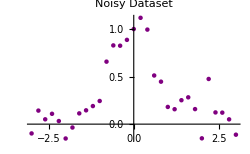

NetChain[…]

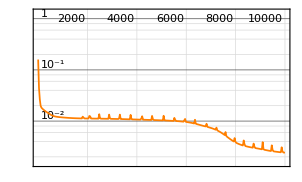
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:10000  rounds:10000  time:19s  examples/s:16398
data | ,,  training examples:31  processed examples:310000  skipped examples:0
method | ,,  ADAMoptimizer  batch size31CPU
round | ,,  loss:2.41×10^-3
 | rounds
loss | -Graphics- | 
 | ]

0.00241152

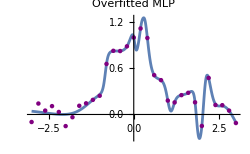

NetChain[…]

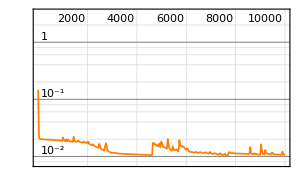
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:10000  rounds:10000  time:18s  examples/s:17663
data | ,,  training examples:31  processed examples:310000  skipped examples:0
method | ,,  ADAMoptimizer  batch size31CPU
round | ,,  loss:1.06×10^-2
 | rounds
loss | -Graphics- | 
 | ]

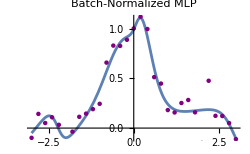

```mathematica
noisyData=Table[x->Exp[-x^2]+RandomVariate[NormalDistribution[0,.15]],{x,-3,3,.2}];

noisyPlot=ListPlot[
List@@@noisyData,
PlotStyle->Purple,
PlotLabel->"Noisy Dataset",
ImageSize->250
]

mlp=NetChain[{150,Tanh,150,Tanh,1}]

mlpTrainingResults=NetTrain[mlp,noisyData,All]
mlpRoundLoss=mlpTrainingResults["RoundLoss"]

overfittedMLP=mlpTrainingResults["TrainedNet"];

Show[
Plot[
overfittedMLP[x],
{x,-3,3},
PlotLabel->"Overfitted MLP",
ImageSize->250
],
noisyPlot
]

batchNormMLP=NetChain[
{
150,BatchNormalizationLayer[],Tanh,
150,BatchNormalizationLayer[],Tanh,
1
}
]

batchNormTrainingResults=NetTrain[batchNormMLP,noisyData,All]

batchNormTrainedNet=batchNormTrainingResults["TrainedNet"];

Show[
Plot[
batchNormTrainedNet[x],
{x,-3,3},
PlotLabel->"Batch-Normalized MLP",
ImageSize->250
],
noisyPlot
]
```

code 5.48

(* The code accomplishes several tasks in the context of neural network training and analysis. It begins by generating synthetic input-output data using a mixture distribution. Then, it defines a neural network architecture with BatchNormalization layers and LogisticSigmoid activations, initializes the network with random weights nd biases, and proceeds to train it using the generated data while monitoring activation output statistics. The code extracts and processes activation output data, calculating mean and standard deviation values for both BatchNormalization and LogisticSigmoid layers. Visualization steps include plotting mean activation values with error bars over training epochs, performing kernel density estimation and visualization, and creating histograms to depict the distribution of activation values for specific layers. BatchNormalization normalizes the inputs to each layer, helping to prevent activations from becoming too large or too small, which can lead to saturation. By normalizing the inputs, BatchNormalization helps to keep the activations within a more stable range, thereby alleviating the saturation problem associated with the logistic sigmoid function. The figures generated by the code illustrate various aspects of the neural network training process and activation behaviors. The first set of figures depicts the mean activation values with error bars over training epochs for both BatchNormalization and LogisticSigmoid layers, showcasing their convergence patterns and variability. Additionally, kernel density estimation plots visualize the distribution of activation values for specific layers, demonstrating the spread and density of activations throughout training. Histograms further elucidate the distribution of activation values for specific LogisticSigmoid layers, offering insights into the diversity and concentration of activations: *)

NetGraph[…]

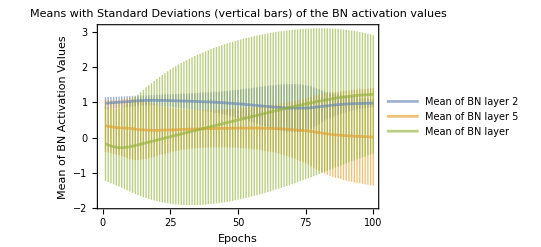

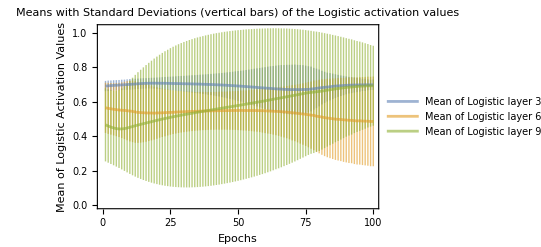

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

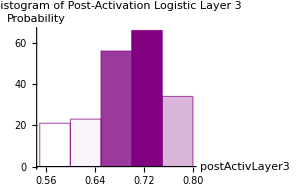
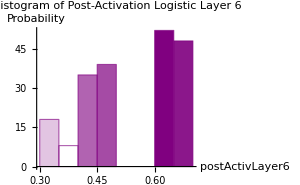
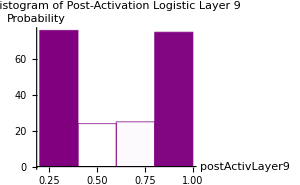

```mathematica
distribution=MixtureDistribution[{1,2},{NormalDistribution[1,5],NormalDistribution[4,6]}];

inputData=RandomVariate[distribution,{2000,200}];
outputData=RandomReal[2,{2000,1}];

neuralNet=NetGraph[
{
2,BatchNormalizationLayer[],LogisticSigmoid,
2,BatchNormalizationLayer[],LogisticSigmoid,
2,BatchNormalizationLayer[],LogisticSigmoid,
1,LogisticSigmoid
},
{1->2->3->4->5->6->7->8->9->10->11},
"Input"->200
];

initializedNet=NetInitialize[
neuralNet,
Method->{"Random","Weights"->1,"Biases"->1},
RandomSeeding->Automatic
]

trainingResults=NetTrain[
initializedNet,
<|"Input"->inputData,"Output"->outputData|>,
All,
MaxTrainingRounds->100,
TrainingProgressMeasurements->{
<|"Measurement"->NetPort[{2,"Output"}],"Interval"->"Round"|>,
<|"Measurement"->NetPort[{5,"Output"}],"Interval"->"Round"|>,
<|"Measurement"->NetPort[{8,"Output"}],"Interval"->"Round"|>,
<|"Measurement"->NetPort[{3,"Output"}],"Interval"->"Round"|>,
<|"Measurement"->NetPort[{6,"Output"}],"Interval"->"Round"|>,
<|"Measurement"->NetPort[{9,"Output"}],"Interval"->"Round"|>
}
];

trainingData=trainingResults["RoundMeasurementsLists"];
{
BNactivationOutputLayer2,
BNactivationOutputLayer5,
BNactivationOutputLayer8,
LogisticactivationOutputLayer3,
LogisticactivationOutputLayer6,
LogisticactivationOutputLayer9
}=Values[trainingData][[{2,3,4,5,6,7}]];

processLayer[output_]:=Module[
{mean,stdDev,meanWithStdDev},
mean=Mean/@output;
stdDev=StandardDeviation/@output;
meanWithStdDev=Around@@@Transpose[{mean,stdDev}];
meanWithStdDev
]

{
meanWithStdDevBNLayer2,
meanWithStdDevBNLayer5,
meanWithStdDevBNLayer8
}=processLayer/@{
BNactivationOutputLayer2,
BNactivationOutputLayer5,
BNactivationOutputLayer8};

{
meanWithStdDevLogisticLayer3,
meanWithStdDevLogisticLayer6,
meanWithStdDevLogisticLayer9
}=processLayer/@{
LogisticactivationOutputLayer3,
LogisticactivationOutputLayer6,
LogisticactivationOutputLayer9};

ListLinePlot[
{
meanWithStdDevBNLayer2,
meanWithStdDevBNLayer5,
meanWithStdDevBNLayer8
},
PlotStyle->{Opacity[0.6],Opacity[0.6],Opacity[0.6]},
PlotRange->Full,
PlotLegends->{
"Mean of BN layer 2",
"Mean of BN layer 5",
"Mean of BN layer "
},
IntervalMarkers->"Bars",
Frame->True,
FrameLabel->{"Epochs","Mean of BN Activation Values"},
PlotLabel->"Means with Standard Deviations (vertical bars)\n of the BN activation values"
]

ListLinePlot[
{
meanWithStdDevLogisticLayer3,
meanWithStdDevLogisticLayer6,
meanWithStdDevLogisticLayer9
},
PlotStyle->{Opacity[0.6],Opacity[0.6],Opacity[0.6]},
PlotRange->Full,PlotLegends->{
"Mean of Logistic layer 3",
"Mean of Logistic layer 6",
"Mean of Logistic layer 9"
},
IntervalMarkers->"Bars",
Frame->True,
FrameLabel->{"Epochs","Mean of Logistic Activation Values"},PlotLabel->"Means with Standard Deviations (vertical bars)\n of the Logistic activation values" ]

createSmoothKernels[layer_]:=Module[
{sk},
sk=SmoothKernelDistribution[#]&/@layer;
Return[sk];
];

{
SKBNactivationLayer2,SKBNactivationLayer5,
SKBNactivationLayer8,SKLogisticactivationLayer3,
SKLogisticactivationLayer6,SKLogisticactivationLayer9
}=createSmoothKernels/@{
BNactivationOutputLayer2,BNactivationOutputLayer5,
BNactivationOutputLayer8,LogisticactivationOutputLayer3,
LogisticactivationOutputLayer6,LogisticactivationOutputLayer9};

Table[
ListLinePlot3D[
Table[
{(#-1),x,PDF[layer[[2]][[#]],x]},
{x,-0.5,1.5,0.01}
]&/@Range[1,20],
Filling->Bottom,
FillingStyle->Opacity[0.75],
Joined->True,
BoxRatios->{1,1,1},
PlotRange->All,
ImageSize->300,
AxesLabel->{"Epocks","Activation values","Density"},
PlotLabel->Style[Row[{"Distributions of Logistic Layer ",layer[[1]]}]]
]
,{layer,{
{"3",SKLogisticactivationLayer3},
{"6",SKLogisticactivationLayer6},
{"9",SKLogisticactivationLayer9}
}
} ]

Table[
Histogram[
Flatten[layer[[3]]],
Automatic,
"Count",
PlotLabel->Style[Row[{"Histogram of ",layer[[2]]}]],AxesLabel->{layer[[1]],"Probability"},ColorFunction->Function[{height},Opacity[height]],
ChartStyle->Purple,
ImageSize->300
],
{layer,
{
{"postActivLayer3","Post-Activation Logistic Layer 3",LogisticactivationOutputLayer3},{"postActivLayer6","Post-Activation Logistic Layer 6",LogisticactivationOutputLayer6},{"postActivLayer9","Post-Activation Logistic Layer 9",LogisticactivationOutputLayer9}
}
}
]
```